```mathematica
m=500;n=50;
```

```mathematica
δ0=1;Γn=1.;
```

```mathematica
Arand=RandomVariate[NormalDistribution[0,√m*δ0/π],{m,m}];
```

```mathematica
H=I*(Arand-Transpose@Arand);
```

```mathematica
wn=√((m*δ0)/(π^2 Γn)*(2-Γn-2 √(1-Γn)))
```

7.11763

```mathematica
W=DiagonalMatrix[ConstantArray[wn,n],0,{m,n}]
```

{{7.11763,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,7.11763,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},496,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}
 |  |  |  |

```mathematica
W=SparseArray[{Band[{1,1}]->wn},{m,n}];
```

```mathematica
heff=H-I π W. Transpose@W;//AbsoluteTiming
```

{0.0039256,Null}

```mathematica
H
```

$Aborted[]

```mathematica
eig=Eigenvalues[Heff]
```

{-6.23744-0.742913 ⅈ,6.23744-0.742913 ⅈ,-3.87165-0.438649 ⅈ,3.87165-0.438649 ⅈ,-3.25427-0.803059 ⅈ,3.25427-0.803059 ⅈ,-1.36514-0.734197 ⅈ,1.36514-0.734197 ⅈ,-1.46847×10^-15-0.817201 ⅈ,-3.27143×10^-16-0.11136 ⅈ}

```mathematica
{Re[#],Im[#]}&/@eig
```

{{-6.23744,-0.742913},{6.23744,-0.742913},{-3.87165,-0.438649},{3.87165,-0.438649},{-3.25427,-0.803059},{3.25427,-0.803059},{-1.36514,-0.734197},{1.36514,-0.734197},{-1.46847×10^-15,-0.817201},{-3.27143×10^-16,-0.11136}}

```mathematica
HW[m_?IntegerQ,n_?IntegerQ]:=Block[{Arand,H,wn,W,δ0=1.,Γn=.2},Arand=RandomVariate[NormalDistribution[0,√m*δ0/π],{m,m}];H=I*(Arand-Transpose@Arand)/√2;wn=√((m*δ0)/(π^2 Γn)*(2-Γn-2 √(1-Γn)));{H,SparseArray[{Band[{1,1}]->wn},{m,n}]}]
```

```mathematica
Heff[H_,W_]:=H-I π W. Transpose@W
```

```mathematica
hwlist=ParallelTable[HW[120,2],50000];//AbsoluteTiming
```

{24.7149,Null}

```mathematica
Hlist=Heff@@@hwlist;//AbsoluteTiming
```

{0.0957001,Null}

```mathematica
eiglist=ParallelTable[Eigenvalues@i,{i,Hlist}];//AbsoluteTiming
```

{0.939199,Null}

#### Γn=1

```mathematica
Graphics[Point[{Re[#],Im[#]}&/@Flatten@eiglist],Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},{-100,0}}]
```

-Graphics-

#### Γn=0.2

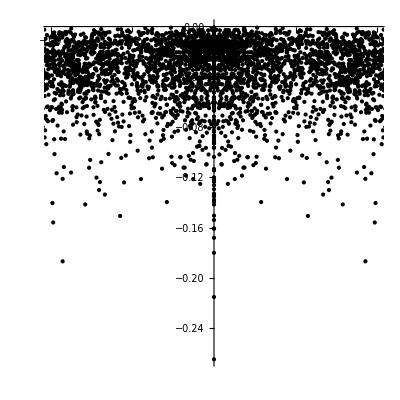

```mathematica
Graphics[Point[{Re[#],Im[#]}&/@Flatten@eiglist],Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},Automatic}]
```

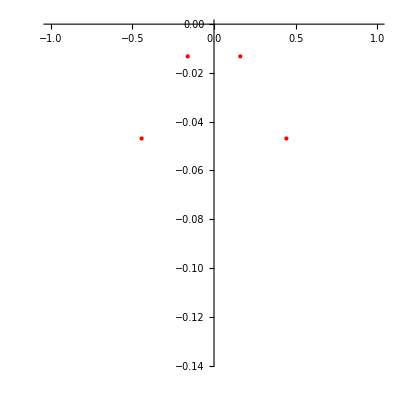
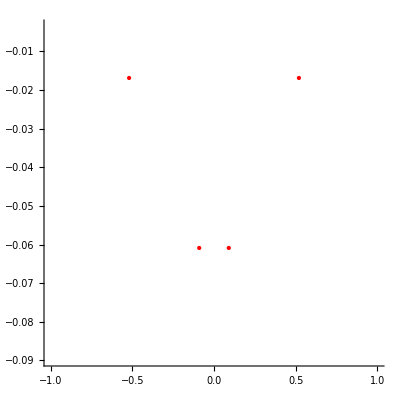
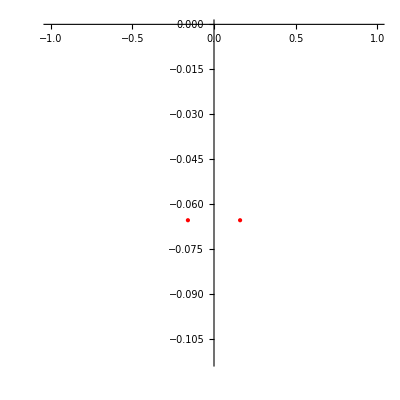
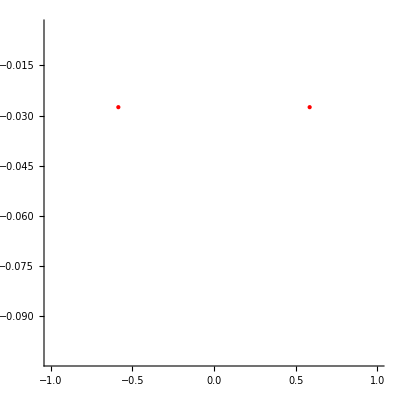
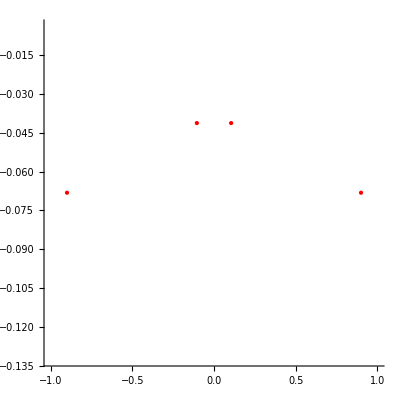
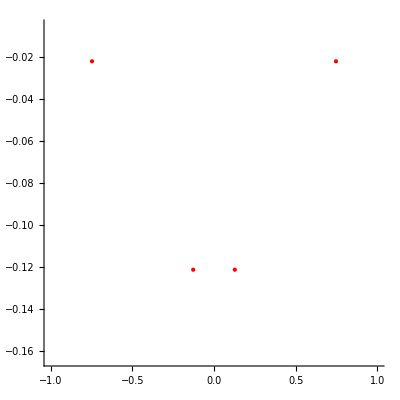
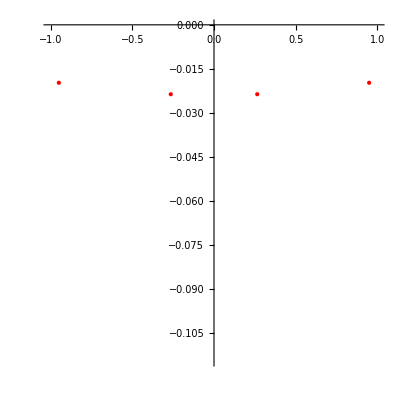
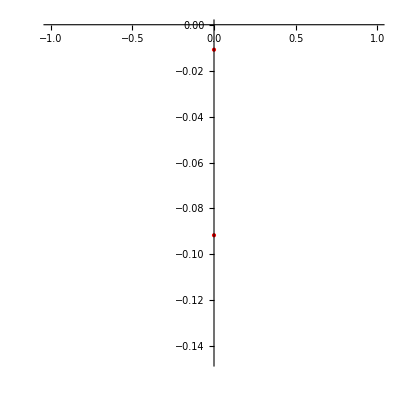

```mathematica
Function[i,Graphics[{Red,PointSize[Large],Point[{Re[#],Im[#]}&/@Eigenvalues[Hlist[[i]]]]},Axes->True,AspectRatio->1,AxesOrigin->{0,0},PlotRange->{{-1,1},All}]]/@Range[1,20]
```

```mathematica
eiglist//Dimensions
```

{1000,120}

```mathematica
gamma=Select[#//Chop,I*Im[#]==#&]&/@eiglist;
```

Eigenvalues::argt: Eigenvalues called with 0 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Eigenvalues::argt will be suppressed during this calculation.

```mathematica
gammas=Sort/@Im/@(gamma/.{}->Sequence[]);
```

{{-0.164423,-0.0191432},{-0.170932,-0.0531918},{-0.017437,-0.00348935},{-0.0431739,-0.01226},{-0.177727,-0.00358513},{-0.036464,-0.00586326},{-0.272647,-0.003359},{-0.0282511,-0.00500917},{-0.0324699,-0.00263402},{-0.11289,-0.00367744},{-0.113535,-0.0238695},{-0.0673403,-0.0450958},{-0.272751,-0.0532384},{-0.0408277,-0.0260026},{-0.219386,-0.00106377},{-0.0431474,-0.00749242},{-0.0974892,-0.0313571},{-0.122194,-0.0171262},{-0.0461143,-0.0219971},{-0.0801134,-0.0273476},{-0.0523823,-0.00143975},{-0.0618403,-0.0345634},{-0.042197,-0.0154805},{-0.0474353,-0.00620932},{-0.0626718,-0.0248594},{-0.239196,-0.0100071},{-0.0330555,-0.00347761},{-0.127299,-0.00706191},{-0.104977,-0.0589264},{-0.0461538,-0.00388653},{-0.101629,-0.0294012},{-0.0757953,-0.0198361},{-0.117074,-0.0116398},{-0.0914992,-0.0162689},{-0.0369966,-0.00220766},{-0.0638628,-0.00649212},{-0.241877,-0.0139839},{-0.0647997,-0.00863136},{-0.0810803,-0.00582372},{-0.0376766,-0.0231094},{-0.117646,-0.0267685},{-0.148351,-0.0500934},{-0.105624,-0.00134889},{-0.229841,-0.0471918},{-0.0312859,-0.00183366},{-0.0117285,-0.000172765},{-0.0423467,-0.0131012},{-0.103928,-0.00527978},{-0.101946,-0.0218565},{-0.0806675,-0.00899979},{-0.0200619,-0.0115067},{-0.170455,-0.0121554},{-0.100263,-0.00866488},{-0.19108,-0.0202027},{-0.0258241,-0.00113894},{-0.0375813,-0.010699},{-0.100194,-0.00565858},{-0.168698,-0.00268998},{-0.0917831,-0.00406056},{-0.0612761,-0.00774169},{-0.0192317,-0.00632593},{-0.0688422,-0.0149406},{-0.0763746,-0.000734183},{-0.210654,-0.0878183},{-0.0760602,-0.0131412},{-0.0934885,-0.00952471},{-0.0758066,-0.0276019},{-0.0748634,-0.0228321},{-0.0302771,-0.00638016},{-0.210924,-0.0191979},{-0.0501912,-0.0115421},{-0.143581,-0.0535154},{-0.0843791,-0.0673135},{-0.0732282,-0.0202948},{-0.0397499,-0.0280787},{-0.044647,-0.000418201},{-0.137895,-0.00458277},{-0.0381778,-0.0232222},{-0.060082,-0.00502848},{-0.109547,-0.0206061},{-0.0898336,-0.0463517},{-0.0924509,-0.046892},{-0.120669,-0.0248628},{-0.0148547,-0.00163034},{-0.0832441,-0.00760867},{-0.028313,-0.00769033},{-0.0894962,-0.0155374},{-0.122543,-0.0299993},{-0.0432163,-0.019585},{-0.0382299,-0.0227606},{-0.115709,-0.00274465},{-0.0345307,-0.0124552},{-0.0754739,-0.00297482},{-0.127625,-0.00034399},{-0.0379397,-0.00355938},{-0.0173893,-0.00209795},{-0.110955,-0.00191849},{-0.139473,-0.0391699},{-0.141071,-0.0296529},{-0.174489,-0.0418643},{-0.0612487,-0.0270388},{-0.0533602,-0.00295601},{-0.09687,-0.0170578},{-0.125899,-0.0017683},{-0.0861972,-0.00102581},{-0.0834428,-0.0650966},{-0.0677213,-0.0199615},{-0.179285,-0.0484108},{-0.0817066,-0.0244302},{-0.190608,-0.00564608},{-0.0595147,-0.00438764},{-0.128463,-0.00230021},{-0.0474505,-0.0241869},{-0.0843573,-0.00972588},{-0.104897,-0.0220461},{-0.0302093,-0.0100242},{-0.0979168,-0.0139388},{-0.0531065,-0.0223069},{-0.0651363,-0.00375391},{-0.226886,-0.00249664},{-0.0629998,-0.0386764},{-0.0753022,-0.0173591},{-0.214954,-0.0151256},{-0.0662849,-0.0197701},{-0.104682,-0.0319236},{-0.0875558,-0.00962752},{-0.141762,-0.0691504},{-0.145513,-0.00796688},{-0.085109,-0.00935344},{-0.106098,-0.03414},{-0.0330536,-0.00859944},{-0.0234438,-0.0145225},{-0.0121506,-0.00639335},{-0.131461,-0.00238548},{-0.128655,-0.00595754},{-0.110511,-0.0336773},{-0.0505018,-0.00412421},{-0.0330963,-0.0102413},{-0.0676716,-0.00625348},{-0.210421,-0.0112162},{-0.0313492,-0.00377312},{-0.069489,-0.0273844},{-0.0526537,-0.0152598},{-0.11775,-0.0126805},{-0.0761001,-0.00934143},{-0.0559324,-0.00336745},{-0.0903823,-0.0331496},{-0.117824,-0.0200586},{-0.0296722,-0.0158065},{-0.133256,-0.0366245},{-0.0506292,-0.0136436},{-0.165131,-0.0268638},{-0.210023,-0.0120584},{-0.119028,-0.0250296},{-0.0303941,-0.00790525},{-0.0509209,-0.0108175},{-0.0904913,-0.0598941},{-0.111223,-0.0528181},{-0.130649,-0.0142148},{-0.108459,-0.0153838},{-0.0306431,-0.000433242},{-0.0753949,-0.0117038},{-0.0288978,-0.00286634},{-0.298873,-0.00629635},{-0.131694,-0.0305122},{-0.184489,-0.0370205},{-0.184149,-0.0110419},{-0.0291928,-0.000215295},{-0.0723212,-0.0204228},{-0.16562,-0.061304},{-0.0182178,-0.013968},{-0.152354,-0.0414333},{-0.0649227,-0.0252184},{-0.0578212,-0.0215721},{-0.0596374,-0.0111786},{-0.0850147,-0.0145379},{-0.0992048,-0.0457727},{-0.02515,-0.00689832},{-0.0716347,-0.00297437},{-0.0991989,-0.00237625},{-0.121457,-0.000742146},{-0.204529,-0.00313524},{-0.086398,-0.0670122},{-0.0825861,-0.0135239},{-0.180128,-0.0952523},{-0.0678456,-0.0124062},{-0.0371279,-0.000359573},{-0.087398,-0.00699187},{-0.10346,-0.0424202},{-0.0647877,-0.00976166},{-0.105468,-0.0193879},{-0.131166,-0.0242006},{-0.213018,-0.0155609},{-0.0648073,-0.00783454},{-0.105934,-0.05093},{-0.0340398,-0.00995969},{-0.0693421,-0.0368547},{-0.0761453,-0.0301173},{-0.0559608,-0.0366709},{-0.0443995,-0.0000846885},{-0.04232,-0.0208653},{-0.0642956,-0.0217912},{-0.147255,-0.0253883},{-0.0702178,-0.0000112938},{-0.13756,-0.0282648},{-0.0719366,-0.00210341},{-0.020905,-0.0170158},{-0.0227417,-0.0161766},{-0.120332,-0.00528396},{-0.103557,-0.07401},{-0.0905627,-0.0538455},{-0.0999591,-0.00392209},{-0.0643139,-0.0293439},{-0.115422,-0.00979417},{-0.0321845,-0.0202519},{-0.0435682,-0.0124854},{-0.0405177,-0.0117025},{-0.0473231,-0.0062932},{-0.0598823,-0.0377787},{-0.0861442,-0.0340873},{-0.163899,-0.00500832},{-0.117897,-0.0423688},{-0.0232405,-0.0064416},{-0.0723308,-0.00812997},{-0.0951204,-0.0325136},{-0.153,-0.0251328},{-0.0522827,-0.0308142},{-0.110965,-0.0277931},{-0.036604,-0.00120803},{-0.0614989,-0.0237734},{-0.0470833,-0.0124645},{-0.105399,-0.015326},{-0.0488755,-0.0132293},{-0.0404115,-0.00785876},{-0.0460649,-0.00400511},{-0.0698264,-0.0144739},{-0.108259,-0.0491355},{-0.10141,-0.00214985},{-0.11,-0.0263539},{-0.0523385,-0.0198799},{-0.0217809,-0.000350371},{-0.055027,-0.0292415},{-0.0706057,-0.0168607},{-0.0801787,-0.0277868},{-0.0374854,-0.00723564},{-0.133958,-0.0170319},{-0.141369,-0.00671962},{-0.0909788,-0.0221682},{-0.0678182,-0.00270075},{-0.127582,-0.00194498},{-0.0892191,-0.0156615},{-0.0265129,-0.00671774},{-0.0751641,-0.0106719},{-0.251843,-0.0157538},{-0.12033,-0.0148618},{-0.0249842,-0.00520241},{-0.1277,-0.000610627},{-0.081233,-0.00672172},{-0.132475,-0.00130934},{-0.0900508,-0.0000213862},{-0.20331,-0.0704174},{-0.143257,-0.00247815},{-0.0811794,-0.011197},{-0.067346,-0.0244493},{-0.0785371,-0.0287172},{-0.0197329,-0.00255768},{-0.058323,-0.00230838},{-0.115411,-0.0142625},{-0.054829,-0.00425612},{-0.0511576,-0.00115243},{-0.0962171,-0.0322578},{-0.123241,-0.0111187},{-0.0371645,-0.016628},{-0.0609116,-0.00577649},{-0.0059116,-0.00112932},{-0.125523,-0.00771638},{-0.0643201,-0.0209034},{-0.0587892,-0.0178864},{-0.105042,-0.0502573},{-0.171692,-0.0114224},{-0.224313,-0.0517943},{-0.0281529,-0.0150642},{-0.0353105,-0.0136321},{-0.16069,-0.009368},{-0.0965698,-0.0122975},{-0.0470924,-0.000173929},{-0.0400846,-0.00402004},{-0.0570095,-0.00250092},{-0.103588,-0.0648833},{-0.149201,-0.0875227},{-0.0988687,-0.0124074},{-0.19094,-0.0103304},{-0.0792343,-0.00993106},{-0.187446,-0.00416604},{-0.0978312,-0.0633671},{-0.139485,-0.0867709},{-0.0304902,-0.00886194},{-0.0726318,-0.0250361},{-0.0641574,-0.0027735},{-0.00959949,-0.00563421},{-0.102738,-0.0205647},{-0.0524031,-0.00865828},{-0.0851775,-0.0627352},{-0.142978,-0.0212719},{-0.0352287,-0.00207434},{-0.0475931,-0.028633},{-0.0439127,-0.0266201},{-0.0411634,-0.0230308},{-0.0457504,-0.0272717},{-0.0421685,-0.0187544},{-0.148544,-0.00236037},{-0.102899,-0.00115689},{-0.0246682,-6.97117×10^-6},{-0.295616,-0.00243834},{-0.0820758,-0.028653},{-0.0674064,-0.0219429},{-0.108614,-0.0103443},{-0.0809096,-0.0291133},{-0.18073,-0.027574},{-0.102186,-0.0215422},{-0.0772877,-0.0116335},{-0.0629738,-0.0104245},{-0.140485,-0.0146042},{-0.0757398,-0.0238847},{-0.148325,-0.0129966},{-0.0471644,-0.00688212},{-0.0797368,-0.0444009},{-0.104535,-0.00184797},{-0.158552,-0.00249714},{-0.0982129,-0.0341984},{-0.0231107,-0.010992},{-0.096821,-0.0370546},{-0.0766487,-0.0354237},{-0.0832698,-0.00867114},{-0.103446,-0.038827},{-0.0992159,-0.035243},{-0.0610397,-0.00535261},{-0.23372,-0.0373175},{-0.32878,-0.0168996},{-0.0797424,-0.0384882},{-0.0731456,-0.0244484},{-0.139502,-0.0407194},{-0.0999708,-0.0179613},{-0.0610288,-0.0151059},{-0.0759511,-0.0000562198},{-0.155805,-0.00512051},{-0.0269244,-0.0147265},{-0.0226835,-0.0123702},{-0.106952,-0.000912625},{-0.165428,-0.00563486},{-0.102975,-0.0497888},{-0.0273339,-0.0075399},{-0.0728939,-0.000840491},{-0.0387974,-0.0052238},{-0.133623,-0.0239036},{-0.0809958,-0.00639992},{-0.0366785,-0.000616455},{-0.0667311,-0.0209065},{-0.0321913,-0.00126082},{-0.107659,-0.000907935},{-0.0638549,-0.0120895},{-0.152282,-0.00839374},{-0.0534423,-0.00680637},{-0.074827,-0.00970902},{-0.136497,-0.00631147},{-0.0989279,-0.00132037},{-0.127353,-0.0315352},{-0.238196,-0.0105151},{-0.0555933,-0.0215582},{-0.149958,-0.027711},{-0.101974,-0.0120704},{-0.0043403,-0.00240434},{-0.0496584,-0.0126181},{-0.0638868,-0.0138459},{-0.0703949,-0.00293152},{-0.0602512,-0.0213174},{-0.116328,-0.00567798},{-0.0622707,-0.00359259},{-0.0312311,-0.0135673},{-0.113894,-0.0184696},{-0.0473721,-0.00893632},{-0.0644459,-0.025382},{-0.138613,-0.0111498},{-0.0494496,-0.0171398},{-0.0752614,-0.00631958},{-0.0943411,-0.0273087},{-0.105127,-0.00641849},{-0.0451642,-0.0131059},{-0.162361,-0.00149929},{-0.176639,-0.0241632},{-0.0340789,-0.0209743},{-0.177572,-0.00570468},{-0.0760524,-0.0300218},{-0.24323,-0.0167563},{-0.15978,-0.101697},{-0.0892408,-0.0121581},{-0.0653841,-0.00136703},{-0.129046,-0.0192211},{-0.0715438,-0.0148693},{-0.0313082,-0.00675057},{-0.0630557,-0.00710335},{-0.137043,-0.0740764},{-0.0825131,-0.0238823},{-0.044133,-0.0310088},{-0.0896991,-0.0104317},{-0.100011,-0.00180339},{-0.032278,-0.00167735},{-0.136345,-0.0422814},{-0.0606836,-0.0243519},{-0.10688,-0.0322464},{-0.0524664,-0.0230907},{-0.164071,-0.0134527},{-0.0816044,-0.0213024},{-0.135319,-0.0138951},{-0.0407404,-0.0258403},{-0.0887703,-0.00763559},{-0.146268,-0.0800708},{-0.319297,-0.00476063},{-0.121452,-0.0459506},{-0.121495,-0.046524},{-0.10537,-0.00262793},{-0.0391727,-0.00249486},{-0.0902376,-0.0113249},{-0.031779,-0.000680089},{-0.0800706,-0.0129911},{-0.0386855,-0.00614699},{-0.0897167,-0.0166987},{-0.0537115,-0.020747},{-0.0171549,-0.0129496},{-0.139354,-0.0133257},{-0.160475,-0.0113352},{-0.132128,-0.0162507},{-0.0740763,-0.0379751},{-0.167795,-0.0221068},{-0.0563609,-0.0257074},{-0.0620956,-0.0184145},{-0.128475,-0.0250478},{-0.0889464,-0.0176109},{-0.188236,-0.0053864},{-0.1086,-0.0329993},{-0.221186,-0.00922423},{-0.0481884,-0.0121647},{-0.103674,-0.0274025},{-0.0790368,-0.00985057},{-0.0398518,-0.000631575},{-0.0956949,-0.00260739},{-0.0631415,-0.0158279},{-0.114316,-0.0101061},{-0.0639129,-0.0110538},{-0.132545,-0.0194209},{-0.0174452,-0.00247023},{-0.0644091,-0.0134103},{-0.127009,-0.0204703},{-0.0611298,-0.0321372},{-0.0463649,-0.0085731},{-0.200259,-0.00939544},{-0.0325495,-0.01095},{-0.0846196,-0.022124},{-0.112529,-0.0229009},{-0.0619177,-0.0154567},{-0.099511,-0.0372472},{-0.0965869,-0.00188352},{-0.135295,-0.0183723},{-0.106312,-0.0178914},{-0.0329559,-0.000247797},{-0.0947786,-0.00843998},{-0.0283872,-0.00755452},{-0.0142524,-0.00936963},{-0.0261566,-0.00341163},{-0.151321,-0.0786634},{-0.0583341,-0.0508697},{-0.149839,-0.0215841},{-0.0712543,-0.0103886},{-0.0359061,-0.0238563},{-0.0498028,-0.0120726},{-0.0903576,-0.0141833},{-0.108601,-0.00825269},{-0.153912,-0.0180322},{-0.0862391,-0.00927895},{-0.0762456,-0.0167474},{-0.076094,-0.0263728},{-0.0606994,-0.0179102},{-0.170001,-0.0194},{-0.047897,-0.00878129},{-0.0583562,-0.0213048},{-0.0452181,-0.0265712},{-0.180427,-0.0733499},{-0.0810693,-0.0131289},{-0.0265852,-0.00280798},{-0.123934,-0.0189102},{-0.231146,-0.0434513},{-0.167077,-0.0204899},{-0.129772,-0.00632571},{-0.0939177,-0.0291569},{-0.100954,-0.0481837},{-0.0659068,-0.00571296},{-0.0338687,-0.014116},{-0.133427,-0.021761},{-0.0364233,-0.00917339},{-0.109735,-0.00284998},{-0.0263582,-0.00154915},{-0.054622,-0.0230986},{-0.03457,-0.0063061},{-0.0345546,-0.0144403},{-0.0445712,-0.00164355},{-0.136753,-0.0132537},{-0.0448375,-0.0116198},{-0.0471875,-0.00826882},{-0.0652176,-0.0252743},{-0.10024,-0.0245205},{-0.0630847,-0.00252477},{-0.030157,-0.00505897},{-0.0598162,-0.0372608},{-0.11214,-0.00198198},{-0.0286529,-0.0070593},{-0.0494016,-0.00893557},{-0.0559388,-0.0214444},{-0.0269186,-0.00390432},{-0.136343,-0.00161995},{-0.106782,-0.0288175},{-0.0545027,-0.0438219},{-0.0209584,-0.00347423},{-0.141371,-0.00870465},{-0.0718462,-0.00485012},{-0.0655069,-0.0207777},{-0.0760228,-0.00553496},{-0.205603,-0.0188275},{-0.0398503,-0.0207633},{-0.0574168,-0.022556},{-0.100279,-0.000335823},{-0.0624652,-0.000600798},{-0.0779448,-0.0318756},{-0.076958,-0.0548707},{-0.0898131,-0.000308863},{-0.14078,-0.038317},{-0.130263,-0.0419364},{-0.0225041,-0.00596233},{-0.0745882,-0.0103486},{-0.163475,-0.0286846},{-0.115232,-0.00527518},{-0.0680541,-0.00983647},{-0.156381,-0.0486194},{-0.034566,-0.00919311},{-0.281713,-0.00218836},{-0.114786,-0.0109227},{-0.084395,-0.00615443},{-0.0476064,-0.0230222},{-0.0693174,-0.00396693},{-0.0819863,-0.00586672},{-0.113541,-0.00749863},{-0.112488,-0.0140305},{-0.0448896,-0.0098305},{-0.105925,-0.00186048},{-0.10057,-0.0078361},{-0.0324009,-0.0218849},{-0.0933538,-0.0358565},{-0.114179,-0.0291036},{-0.0602109,-0.0340913},{-0.0334784,-0.0207894},{-0.0204118,-0.0136749},{-0.0915293,-0.00907685},{-0.103408,-0.0228053},{-0.141069,-0.063388},{-0.0249114,-0.00761601},{-0.0779134,-0.0163551},{-0.131441,-0.00286559},{-0.0403232,-0.0201981},{-0.036173,-0.00343339},{-0.0540911,-0.00137275},{-0.0592508,-0.0250783},{-0.0631112,-0.0254499},{-0.156553,-0.0136309},{-0.100058,-0.0413626},{-0.128376,-0.0117327},{-0.0785865,-0.0150413},{-0.0756409,-0.000502149},{-0.0316683,-0.000795712},{-0.123587,-0.0394115},{-0.0761199,-0.00579625},{-0.0512767,-0.000303793},{-0.089076,-0.0237749},{-0.115869,-0.0407927},{-0.0720607,-0.00302846},{-0.0340197,-0.00456229},{-0.0520253,-0.00863422},{-0.0171166,-0.00244913},{-0.0685434,-0.0124757},{-0.0510193,-0.00826253},{-0.132289,-0.0100563},{-0.101471,-0.032009},{-0.044579,-0.0176238},{-0.0736166,-0.0627239},{-0.0624211,-0.017517},{-0.0636434,-0.0247792},{-0.0877962,-0.0729494},{-0.0551228,-0.0172033},{-0.0692897,-0.0473887},{-0.127853,-0.0203192},{-0.148143,-0.0394553},{-0.0678006,-0.0259373},{-0.0344646,-0.0104628},{-0.0886327,-0.000649173},{-0.105955,-0.0209324},{-0.0237575,-0.00109512},{-0.0533682,-0.016651},{-0.0744393,-0.00359049},{-0.119931,-0.0505667},{-0.0878442,-0.0335172},{-0.0916777,-0.0239812},{-0.0682975,-0.00274733},{-0.0973709,-0.0516819},{-0.0567417,-0.00669891},{-0.0478999,-0.0110165},{-0.0832568,-0.00643474},{-0.0928977,-0.00488619},{-0.114239,-0.0450974},{-0.110023,-0.0217082},{-0.0597752,-0.000815162},{-0.0942686,-0.0080266},{-0.0883912,-0.0069665},{-0.0385462,-0.00157653},{-0.106659,-0.0306785},{-0.128139,-0.00720145},{-0.207269,-0.0333395},{-0.0857404,-0.027604},{-0.0616892,-0.0102246},{-0.0268434,-0.0184066},{-0.0924307,-0.0288007},{-0.0427689,-0.0095605},{-0.088817,-0.0681106},{-0.0594765,-0.00282228},{-0.0731348,-0.0133697},{-0.100926,-0.0222078},{-0.180102,-0.0565401},{-0.0364602,-0.00300102},{-0.121485,-0.00105945},{-0.0856688,-0.00486131},{-0.054621,-0.00564984},{-0.120517,-0.0610673},{-0.0809838,-0.0332083},{-0.0340171,-0.012978},{-0.0898366,-0.00679455},{-0.111684,-0.0172929},{-0.0352098,-0.0115436},{-0.07818,-0.0121333},{-0.0961466,-0.0188256},{-0.115557,-0.00813535},{-0.075727,-0.0401116},{-0.137115,-0.000899247},{-0.13236,-0.00926255},{-0.0688952,-0.0163204},{-0.110311,-0.00280589},{-0.0870946,-0.010466},{-0.0836589,-0.024208},{-0.0826514,-0.0195938},{-0.239885,-0.0300997},{-0.0714081,-0.00520754},{-0.164922,-0.017201},{-0.105215,-0.00932902},{-0.0422893,-0.0110144},{-0.0769859,-0.0040889},{-0.0548343,-0.0122136},{-0.0336698,-0.00580569},{-0.0528073,-0.000453996},{-0.0944872,-0.00334269},{-0.0953929,-0.0108173},{-0.0454939,-0.0198155},{-0.0781499,-0.0177115},{-0.0146127,-0.000447546},{-0.0584072,-0.034402},{-0.228602,-0.0155975},{-0.0482806,-0.00788188},{-0.0394278,-0.024885},{-0.039141,-0.00806502},{-0.120211,-0.0131886},{-0.0941569,-0.022269},{-0.0657426,-0.0381109},{-0.0447159,-0.000329763},{-0.0237832,-0.00323488},{-0.0162449,-0.0017864},{-0.0851766,-0.0380702},{-0.0289085,-0.0162823},{-0.130054,-0.0379746},{-0.137192,-0.0291603},{-0.0335499,-0.0187778},{-0.0985927,-0.00965896},{-0.0697393,-0.0280784},{-0.0340375,-0.0138553},{-0.170972,-0.00125046},{-0.0535601,-0.0264846},{-0.100623,-0.000198178},{-0.0421078,-0.0068149},{-0.0494442,-0.00231278},{-0.0352465,-0.0147548},{-0.0890749,-0.0384833},{-0.244961,-0.0126721},{-0.0601451,-0.00545558},{-0.119971,-0.00489034},{-0.0763339,-0.00998313},{-0.0327159,-0.00834545},{-0.137626,-0.0738445},{-0.0865561,-0.0125733},{-0.0758564,-0.0444789},{-0.0266736,-0.00333232},{-0.103907,-0.0214842},{-0.0948257,-0.0153164},{-0.273661,-0.0548822},{-0.0319527,-0.00304081},{-0.0860206,-0.0312182},{-0.171641,-0.00032916},{-0.0826861,-0.00371946},{-0.0740561,-0.00116174},{-0.110545,-0.0103406},{-0.0770386,-0.00455838},{-0.0611752,-0.00751991},{-0.0456732,-0.0254874},{-0.0816616,-0.00260163},{-0.133754,-0.0171197},{-0.0857033,-0.0129315},{-0.113766,-0.021356},{-0.0704786,-0.00236098},{-0.0589181,-0.0249296},{-0.150274,-0.0110377},{-0.0952989,-0.00415966},{-0.0469017,-0.00678188},{-0.0909961,-0.0402305},{-0.144714,-0.0562243},{-0.0299202,-0.0255706},{-0.108676,-0.0216245},{-0.193467,-0.0162393},{-0.0245655,-0.00678359},{-0.0588591,-0.00459865},{-0.123519,-0.0121291},{-0.0250859,-0.0111326},{-0.181487,-0.0482394},{-0.248302,-0.00178135},{-0.149488,-0.0193037},{-0.0773606,-0.00685338},{-0.177008,-0.0260942},{-0.0664773,-0.0460257},{-0.0404248,-0.0136905},{-0.132544,-0.000127718},{-0.215428,-0.0615439},{-0.0545886,-0.0138198},{-0.10161,-0.0384381},{-0.0812876,-0.000978767},{-0.0859645,-0.0192387},{-0.199772,-0.0268308},{-0.0230432,-0.00712829},{-0.061061,-0.0166214},{-0.053141,-0.00526855},{-0.056039,-0.000240152},{-0.0363765,-0.000137746},{-0.0630655,-0.0497407},{-0.0844835,-0.0135313},{-0.0507048,-0.0201104},{-0.124257,-0.04772},{-0.0826564,-0.0414167},{-0.227089,-0.00235883},{-0.112782,-0.0243665},{-0.209548,-0.00497582},{-0.134873,-0.0223302},{-0.0656959,-0.0234073},{-0.0783523,-0.000795082},{-0.1718,-0.122929},{-0.152559,-0.00331766},{-0.0699484,-0.00348352},{-0.134997,-0.000399832}}

```mathematica
imlist=Flatten@Position[gamma,_?(#≠{}&)];
```

{6,8,12,22,25,50,64,75,76,102,151,163,167,170,175,181,198,199,224,252,260,277,298,306,356,394,399,425,442,445,464,490,524,554,567,569,576,579,588,589,590,595,617,635,640,647,648,658,679,703,704,708,710,711,724,739,765,766,811,814,844,851,881,921,931,934,982,992,995,1023,1038,1050,1062,1096,1123,1128,1163,1179,1210,1242,1254,1285,1292,1316,1317,1320,1328,1334,1337,1341,1359,1367,1377,1390,1391,1400,1405,1407,1415,1426,1430,1437,1451,1466,1467,1481,1486,1511,1518,1558,1572,1576,1579,1616,1657,1666,1671,1681,1686,1729,1737,1758,1763,1766,1771,1796,1810,1816,1823,1832,1845,1927,1977,1981,1996,1997,2019,2072,2088,2094,2095,2099,2109,2117,2122,2125,2142,2143,2146,2154,2184,2188,2218,2225,2254,2288,2300,2302,2308,2314,2317,2325,2332,2346,2358,2385,2386,2389,2396,2399,2434,2451,2460,2465,2480,2486,2507,2508,2545,2568,2626,2636,2648,2708,2721,2735,2741,2769,2782,2791,2800,2801,2807,2827,2830,2850,2852,2867,2892,2920,2921,2930,2938,2949,2955,2966,2985,3004,3036,3043,3069,3074,3080,3086,3095,3127,3141,3152,3165,3166,3190,3199,3228,3238,3251,3254,3281,3318,3337,3354,3356,3357,3368,3393,3397,3406,3420,3436,3449,3477,3483,3500,3512,3523,3539,3546,3564,3567,3575,3597,3598,3624,3672,3674,3677,3679,3687,3696,3722,3729,3734,3738,3741,3751,3772,3774,3826,3839,3842,3868,3885,3907,3910,3927,3932,3936,3963,3975,3981,4006,4010,4012,4014,4029,4044,4052,4066,4068,4071,4097,4113,4114,4147,4152,4161,4192,4211,4222,4230,4239,4262,4280,4299,4301,4320,4329,4331,4333,4362,4372,4388,4407,4417,4421,4439,4441,4457,4476,4492,4501,4517,4548,4554,4559,4565,4569,4572,4579,4601,4605,4621,4636,4639,4648,4655,4657,4679,4720,4724,4736,4742,4780,4792,4797,4806,4881,4886,4915,4918,4936,4953,4955,4957,4970,4980,4984,4991,4999,5012,5013,5018,5025,5045,5062,5075,5077,5080,5087,5101,5172,5195,5198,5216,5218,5230,5266,5285,5297,5302,5335,5343,5363,5368,5369,5400,5422,5431,5455,5477,5509,5573,5578,5583,5592,5607,5613,5618,5621,5636,5645,5652,5672,5714,5718,5721,5727,5732,5734,5743,5774,5785,5810,5812,5818,5821,5835,5889,5919,5931,5936,5938,5942,5949,5951,5969,5970,5985,5993,5995,6002,6005,6069,6089,6092,6098,6118,6150,6174,6189,6214,6217,6241,6283,6303,6305,6306,6311,6337,6343,6349,6367,6368,6373,6377,6378,6388,6425,6444,6449,6450,6467,6485,6487,6492,6495,6517,6523,6535,6547,6556,6570,6587,6591,6592,6598,6599,6600,6610,6640,6650,6657,6666,6676,6678,6691,6695,6701,6705,6725,6729,6744,6756,6764,6775,6785,6799,6813,6817,6870,6872,6876,6877,6919,6932,6951,6963,6964,6966,6979,6990,7003,7006,7007,7015,7034,7038,7047,7048,7050,7059,7061,7076,7093,7108,7109,7185,7195,7211,7234,7240,7316,7342,7387,7414,7441,7442,7446,7448,7479,7487,7506,7523,7539,7549,7555,7592,7599,7600,7603,7607,7619,7633,7636,7639,7640,7644,7645,7649,7686,7703,7706,7718,7735,7749,7751,7754,7763,7771,7772,7793,7795,7807,7820,7829,7832,7837,7841,7842,7843,7876,7880,7910,7916,7943,7945,7956,7959,7965,7976,7985,7990,7994,7999,8007,8018,8036,8048,8053,8058,8080,8091,8099,8112,8117,8120,8122,8127,8130,8136,8139,8156,8163,8165,8169,8180,8185,8199,8217,8222,8237,8240,8241,8263,8278,8296,8311,8325,8328,8335,8389,8418,8427,8429,8434,8437,8442,8464,8472,8477,8490,8491,8494,8551,8575,8655,8659,8677,8682,8728,8747,8752,8758,8761,8769,8775,8789,8792,8795,8798,8799,8800,8843,8850,8853,8866,8876,8880,8881,8916,8932,8948,8964,8969,8970,8981,8986,9000,9004,9012,9021,9026,9033,9038,9039,9041,9042,9050,9058,9060,9065,9067,9072,9095,9099,9105,9123,9125,9132,9147,9153,9163,9170,9178,9205,9212,9220,9237,9245,9252,9264,9268,9270,9277,9279,9321,9322,9327,9340,9371,9387,9453,9466,9519,9529,9533,9541,9544,9552,9574,9584,9596,9599,9603,9606,9620,9622,9626,9627,9638,9643,9658,9700,9710,9714,9724,9725,9726,9757,9759,9769,9771,9775,9777,9788,9793,9828,9844,9851,9881,9897,9903,9915,9927,9938,9962,9975,9990,9995}

```mathematica
cond=ParallelTable[Chop@G[x,hwlist[[i,1]],W1],{i,imlist},{x,-.05,.05,.001}];
```

```mathematica
condmean=Mean/@cond;
```

```mathematica
gc=MapThread[Append[#1,#2]&,{gammas,condmean}]
```

{{-0.164423,-0.0191432,1.21274},{-0.170932,-0.0531918,0.199104},{-0.017437,-0.00348935,0.429801},{-0.0431739,-0.01226,0.618757},{-0.177727,-0.00358513,1.66675},{-0.036464,-0.00586326,0.743174},{-0.272647,-0.003359,1.80265},{-0.0282511,-0.00500917,1.07578},{-0.0324699,-0.00263402,1.30497},{-0.11289,-0.00367744,1.57986},{-0.113535,-0.0238695,1.04023},{-0.0673403,-0.0450958,0.268943},{-0.272751,-0.0532384,0.550291},{-0.0408277,-0.0260026,0.153596},{-0.219386,-0.00106377,1.93635},{-0.0431474,-0.00749242,0.801297},{-0.0974892,-0.0313571,0.412779},{-0.122194,-0.0171262,1.39345},{-0.0461143,-0.0219971,0.619695},{-0.0801134,-0.0273476,1.26538},{-0.0523823,-0.00143975,1.55789},{-0.0618403,-0.0345634,0.619117},{-0.042197,-0.0154805,1.41168},{-0.0474353,-0.00620932,1.01648},{-0.0626718,-0.0248594,1.3484},{-0.239196,-0.0100071,1.36223},{-0.0330555,-0.00347761,1.23392},{-0.127299,-0.00706191,1.41454},{-0.104977,-0.0589264,0.06216},{-0.0461538,-0.00388653,1.10387},{-0.101629,-0.0294012,0.51789},{-0.0757953,-0.0198361,0.49119},{-0.117074,-0.0116398,1.496},{-0.0914992,-0.0162689,1.04304},{-0.0369966,-0.00220766,1.09885},{-0.0638628,-0.00649212,1.22103},{-0.241877,-0.0139839,1.16006},{-0.0647997,-0.00863136,1.39592},{-0.0810803,-0.00582372,1.67224},{-0.0376766,-0.0231094,1.02438},{-0.117646,-0.0267685,0.490448},{-0.148351,-0.0500934,0.305383},{-0.105624,-0.00134889,1.82308},{-0.229841,-0.0471918,0.651884},{-0.0312859,-0.00183366,1.27997},{-0.0117285,-0.000172765,0.59493},{-0.0423467,-0.0131012,1.45454},{-0.103928,-0.00527978,1.69924},{-0.101946,-0.0218565,0.582962},{-0.0806675,-0.00899979,1.29129},{-0.0200619,-0.0115067,0.0962007},{-0.170455,-0.0121554,1.42672},{-0.100263,-0.00866488,1.15508},{-0.19108,-0.0202027,0.812248},{-0.0258241,-0.00113894,1.10745},{-0.0375813,-0.010699,0.525822},{-0.100194,-0.00565858,1.37569},{-0.168698,-0.00268998,1.7331},{-0.0917831,-0.00406056,1.49487},{-0.0612761,-0.00774169,1.5864},{-0.0192317,-0.00632593,0.454877},{-0.0688422,-0.0149406,1.4377},{-0.0763746,-0.000734183,1.71277},{-0.210654,-0.0878183,0.237781},{-0.0760602,-0.0131412,1.36412},{-0.0934885,-0.00952471,1.45099},{-0.0758066,-0.0276019,0.550437},{-0.0748634,-0.0228321,0.676832},{-0.0302771,-0.00638016,1.10264},{-0.210924,-0.0191979,0.932593},{-0.0501912,-0.0115421,1.13737},{-0.143581,-0.0535154,0.142211},{-0.0843791,-0.0673135,0.598324},{-0.0732282,-0.0202948,0.924715},{-0.0397499,-0.0280787,0.585572},{-0.044647,-0.000418201,1.49716},{-0.137895,-0.00458277,1.57834},{-0.0381778,-0.0232222,0.577485},{-0.060082,-0.00502848,1.27053},{-0.109547,-0.0206061,0.625292},{-0.0898336,-0.0463517,0.938617},{-0.0924509,-0.046892,0.920029},{-0.120669,-0.0248628,0.756236},{-0.0148547,-0.00163034,0.766062},{-0.0832441,-0.00760867,1.60078},{-0.028313,-0.00769033,1.03444},{-0.0894962,-0.0155374,0.863252},{-0.122543,-0.0299993,0.887401},{-0.0432163,-0.019585,0.619025},{-0.0382299,-0.0227606,0.767947},{-0.115709,-0.00274465,1.67049},{-0.0345307,-0.0124552,1.04572},{-0.0754739,-0.00297482,1.64479},{-0.127625,-0.00034399,1.8857},{-0.0379397,-0.00355938,1.33315},{-0.0173893,-0.00209795,0.927463},{-0.110955,-0.00191849,1.72103},{-0.139473,-0.0391699,0.435972},{-0.141071,-0.0296529,0.527868},{-0.174489,-0.0418643,0.752096},{-0.0612487,-0.0270388,0.414171},{-0.0533602,-0.00295601,1.27372},{-0.09687,-0.0170578,1.21565},{-0.125899,-0.0017683,1.77311},{-0.0861972,-0.00102581,1.74628},{-0.0834428,-0.0650966,0.652556},{-0.0677213,-0.0199615,1.14907},{-0.179285,-0.0484108,0.247284},{-0.0817066,-0.0244302,1.18785},{-0.190608,-0.00564608,1.56562},{-0.0595147,-0.00438764,1.40459},{-0.128463,-0.00230021,1.72263},{-0.0474505,-0.0241869,1.2174},{-0.0843573,-0.00972588,1.05177},{-0.104897,-0.0220461,1.19909},{-0.0302093,-0.0100242,1.17479},{-0.0979168,-0.0139388,1.44662},{-0.0531065,-0.0223069,1.09221},{-0.0651363,-0.00375391,1.5815},{-0.226886,-0.00249664,1.77711},{-0.0629998,-0.0386764,0.765878},{-0.0753022,-0.0173591,1.15974},{-0.214954,-0.0151256,1.29435},{-0.0662849,-0.0197701,0.456745},{-0.104682,-0.0319236,0.461423},{-0.0875558,-0.00962752,1.18479},{-0.141762,-0.0691504,0.199094},{-0.145513,-0.00796688,1.37493},{-0.085109,-0.00935344,1.1277},{-0.106098,-0.03414,0.282395},{-0.0330536,-0.00859944,1.08161},{-0.0234438,-0.0145225,1.26316},{-0.0121506,-0.00639335,0.088208},{-0.131461,-0.00238548,1.76783},{-0.128655,-0.00595754,1.42858},{-0.110511,-0.0336773,0.312835},{-0.0505018,-0.00412421,1.14709},{-0.0330963,-0.0102413,0.706588},{-0.0676716,-0.00625348,1.38744},{-0.210421,-0.0112162,1.22676},{-0.0313492,-0.00377312,1.12737},{-0.069489,-0.0273844,1.24615},{-0.0526537,-0.0152598,1.32418},{-0.11775,-0.0126805,1.50804},{-0.0761001,-0.00934143,1.22425},{-0.0559324,-0.00336745,1.50624},{-0.0903823,-0.0331496,0.973052},{-0.117824,-0.0200586,1.17107},{-0.0296722,-0.0158065,1.3781},{-0.133256,-0.0366245,0.8288},{-0.0506292,-0.0136436,0.908586},{-0.165131,-0.0268638,1.06451},{-0.210023,-0.0120584,1.33257},{-0.119028,-0.0250296,0.901461},{-0.0303941,-0.00790525,0.667023},{-0.0509209,-0.0108175,1.33219},{-0.0904913,-0.0598941,0.750843},{-0.111223,-0.0528181,0.694333},{-0.130649,-0.0142148,0.986997},{-0.108459,-0.0153838,1.19136},{-0.0306431,-0.000433242,1.23842},{-0.0753949,-0.0117038,0.94567},{-0.0288978,-0.00286634,1.18665},{-0.298873,-0.00629635,1.68472},{-0.131694,-0.0305122,0.585553},{-0.184489,-0.0370205,0.444794},{-0.184149,-0.0110419,1.23547},{-0.0291928,-0.000215295,1.1911},{-0.0723212,-0.0204228,0.817092},{-0.16562,-0.061304,0.16694},{-0.0182178,-0.013968,0.799152},{-0.152354,-0.0414333,0.324573},{-0.0649227,-0.0252184,1.05774},{-0.0578212,-0.0215721,1.28313},{-0.0596374,-0.0111786,0.783793},{-0.0850147,-0.0145379,0.984289},{-0.0992048,-0.0457727,0.367196},{-0.02515,-0.00689832,1.24238},{-0.0716347,-0.00297437,1.47879},{-0.0991989,-0.00237625,1.75646},{-0.121457,-0.000742146,1.87242},{-0.204529,-0.00313524,1.79353},{-0.086398,-0.0670122,0.613438},{-0.0825861,-0.0135239,1.23356},{-0.180128,-0.0952523,0.134397},{-0.0678456,-0.0124062,0.772751},{-0.0371279,-0.000359573,1.32908},{-0.087398,-0.00699187,1.59918},{-0.10346,-0.0424202,0.201637},{-0.0647877,-0.00976166,1.54803},{-0.105468,-0.0193879,0.658944},{-0.131166,-0.0242006,0.740681},{-0.213018,-0.0155609,1.19469},{-0.0648073,-0.00783454,1.34791},{-0.105934,-0.05093,0.560757},{-0.0340398,-0.00995969,0.570054},{-0.0693421,-0.0368547,1.0893},{-0.0761453,-0.0301173,0.931689},{-0.0559608,-0.0366709,1.23736},{-0.0443995,-0.0000846885,1.44299},{-0.04232,-0.0208653,1.12617},{-0.0642956,-0.0217912,0.464627},{-0.147255,-0.0253883,1.15577},{-0.0702178,-0.0000112938,1.712},{-0.13756,-0.0282648,0.693965},{-0.0719366,-0.00210341,1.55414},{-0.020905,-0.0170158,0.992629},{-0.0227417,-0.0161766,0.0631184},{-0.120332,-0.00528396,1.69732},{-0.103557,-0.07401,0.231976},{-0.0905627,-0.0538455,0.529204},{-0.0999591,-0.00392209,1.52061},{-0.0643139,-0.0293439,1.22635},{-0.115422,-0.00979417,1.16747},{-0.0321845,-0.0202519,0.479002},{-0.0435682,-0.0124854,0.6964},{-0.0405177,-0.0117025,1.0976},{-0.0473231,-0.0062932,1.32163},{-0.0598823,-0.0377787,0.52162},{-0.0861442,-0.0340873,1.06903},{-0.163899,-0.00500832,1.67531},{-0.117897,-0.0423688,0.807694},{-0.0232405,-0.0064416,0.815424},{-0.0723308,-0.00812997,1.56629},{-0.0951204,-0.0325136,0.29014},{-0.153,-0.0251328,0.861551},{-0.0522827,-0.0308142,0.979644},{-0.110965,-0.0277931,0.507944},{-0.036604,-0.00120803,1.29965},{-0.0614989,-0.0237734,0.806671},{-0.0470833,-0.0124645,1.18822},{-0.105399,-0.015326,1.41369},{-0.0488755,-0.0132293,1.46297},{-0.0404115,-0.00785876,0.877746},{-0.0460649,-0.00400511,1.07413},{-0.0698264,-0.0144739,1.38435},{-0.108259,-0.0491355,0.517545},{-0.10141,-0.00214985,1.70928},{-0.11,-0.0263539,0.583391},{-0.0523385,-0.0198799,0.627303},{-0.0217809,-0.000350371,1.00713},{-0.055027,-0.0292415,0.943004},{-0.0706057,-0.0168607,0.604042},{-0.0801787,-0.0277868,1.257},{-0.0374854,-0.00723564,1.32952},{-0.133958,-0.0170319,1.06589},{-0.141369,-0.00671962,1.59355},{-0.0909788,-0.0221682,0.636676},{-0.0678182,-0.00270075,1.44412},{-0.127582,-0.00194498,1.73104},{-0.0892191,-0.0156615,1.01353},{-0.0265129,-0.00671774,0.472325},{-0.0751641,-0.0106719,1.00313},{-0.251843,-0.0157538,1.04674},{-0.12033,-0.0148618,1.38256},{-0.0249842,-0.00520241,0.888501},{-0.1277,-0.000610627,1.85254},{-0.081233,-0.00672172,1.39745},{-0.132475,-0.00130934,1.83416},{-0.0900508,-0.0000213862,1.80219},{-0.20331,-0.0704174,0.366997},{-0.143257,-0.00247815,1.75202},{-0.0811794,-0.011197,0.969781},{-0.067346,-0.0244493,1.01392},{-0.0785371,-0.0287172,1.23938},{-0.0197329,-0.00255768,1.01103},{-0.058323,-0.00230838,1.63413},{-0.115411,-0.0142625,1.18742},{-0.054829,-0.00425612,1.59187},{-0.0511576,-0.00115243,1.45816},{-0.0962171,-0.0322578,0.908161},{-0.123241,-0.0111187,1.46877},{-0.0371645,-0.016628,1.4134},{-0.0609116,-0.00577649,1.49835},{-0.0059116,-0.00112932,0.356283},{-0.125523,-0.00771638,1.65249},{-0.0643201,-0.0209034,0.826611},{-0.0587892,-0.0178864,0.700057},{-0.105042,-0.0502573,0.51484},{-0.171692,-0.0114224,1.44509},{-0.224313,-0.0517943,0.326774},{-0.0281529,-0.0150642,0.145035},{-0.0353105,-0.0136321,1.05596},{-0.16069,-0.009368,1.48874},{-0.0965698,-0.0122975,1.2559},{-0.0470924,-0.000173929,1.52586},{-0.0400846,-0.00402004,1.41129},{-0.0570095,-0.00250092,1.40776},{-0.103588,-0.0648833,0.471369},{-0.149201,-0.0875227,0.194676},{-0.0988687,-0.0124074,0.9965},{-0.19094,-0.0103304,1.35616},{-0.0792343,-0.00993106,1.02716},{-0.187446,-0.00416604,1.73403},{-0.0978312,-0.0633671,0.0666806},{-0.139485,-0.0867709,0.46395},{-0.0304902,-0.00886194,0.651106},{-0.0726318,-0.0250361,0.382872},{-0.0641574,-0.0027735,1.43708},{-0.00959949,-0.00563421,0.257922},{-0.102738,-0.0205647,1.18799},{-0.0524031,-0.00865828,0.84357},{-0.0851775,-0.0627352,0.0295182},{-0.142978,-0.0212719,1.26079},{-0.0352287,-0.00207434,1.35306},{-0.0475931,-0.028633,1.36299},{-0.0439127,-0.0266201,0.484258},{-0.0411634,-0.0230308,0.14498},{-0.0457504,-0.0272717,0.224483},{-0.0421685,-0.0187544,1.44139},{-0.148544,-0.00236037,1.75993},{-0.102899,-0.00115689,1.73558},{-0.0246682,-6.97117×10^-6,1.0683},{-0.295616,-0.00243834,1.84208},{-0.0820758,-0.028653,0.630504},{-0.0674064,-0.0219429,1.34787},{-0.108614,-0.0103443,1.17995},{-0.0809096,-0.0291133,0.983871},{-0.18073,-0.027574,0.646634},{-0.102186,-0.0215422,0.914902},{-0.0772877,-0.0116335,0.864259},{-0.0629738,-0.0104245,1.25657},{-0.140485,-0.0146042,1.1051},{-0.0757398,-0.0238847,1.1744},{-0.148325,-0.0129966,1.13179},{-0.0471644,-0.00688212,1.48132},{-0.0797368,-0.0444009,1.01495},{-0.104535,-0.00184797,1.79621},{-0.158552,-0.00249714,1.79233},{-0.0982129,-0.0341984,0.374971},{-0.0231107,-0.010992,1.14134},{-0.096821,-0.0370546,0.266776},{-0.0766487,-0.0354237,1.14641},{-0.0832698,-0.00867114,1.61164},{-0.103446,-0.038827,0.726704},{-0.0992159,-0.035243,0.451499},{-0.0610397,-0.00535261,1.27998},{-0.23372,-0.0373175,0.720279},{-0.32878,-0.0168996,1.13448},{-0.0797424,-0.0384882,0.485715},{-0.0731456,-0.0244484,0.639259},{-0.139502,-0.0407194,0.59019},{-0.0999708,-0.0179613,1.30744},{-0.0610288,-0.0151059,1.49687},{-0.0759511,-0.0000562198,1.74343},{-0.155805,-0.00512051,1.61189},{-0.0269244,-0.0147265,1.17184},{-0.0226835,-0.0123702,1.10145},{-0.106952,-0.000912625,1.81018},{-0.165428,-0.00563486,1.64694},{-0.102975,-0.0497888,0.116091},{-0.0273339,-0.0075399,0.522338},{-0.0728939,-0.000840491,1.71604},{-0.0387974,-0.0052238,0.842985},{-0.133623,-0.0239036,0.600613},{-0.0809958,-0.00639992,1.30537},{-0.0366785,-0.000616455,1.31233},{-0.0667311,-0.0209065,1.39921},{-0.0321913,-0.00126082,1.15758},{-0.107659,-0.000907935,1.81536},{-0.0638549,-0.0120895,1.48064},{-0.152282,-0.00839374,1.63412},{-0.0534423,-0.00680637,1.01308},{-0.074827,-0.00970902,1.24628},{-0.136497,-0.00631147,1.57836},{-0.0989279,-0.00132037,1.77328},{-0.127353,-0.0315352,0.764398},{-0.238196,-0.0105151,1.51278},{-0.0555933,-0.0215582,1.40086},{-0.149958,-0.027711,0.559904},{-0.101974,-0.0120704,1.01171},{-0.0043403,-0.00240434,0.383236},{-0.0496584,-0.0126181,1.44867},{-0.0638868,-0.0138459,1.43506},{-0.0703949,-0.00293152,1.65985},{-0.0602512,-0.0213174,1.29351},{-0.116328,-0.00567798,1.71095},{-0.0622707,-0.00359259,1.35855},{-0.0312311,-0.0135673,0.355036},{-0.113894,-0.0184696,0.786983},{-0.0473721,-0.00893632,1.17109},{-0.0644459,-0.025382,0.688252},{-0.138613,-0.0111498,1.40209},{-0.0494496,-0.0171398,0.454675},{-0.0752614,-0.00631958,1.55732},{-0.0943411,-0.0273087,0.370109},{-0.105127,-0.00641849,1.45424},{-0.0451642,-0.0131059,0.64815},{-0.162361,-0.00149929,1.86147},{-0.176639,-0.0241632,0.807125},{-0.0340789,-0.0209743,0.461951},{-0.177572,-0.00570468,1.53361},{-0.0760524,-0.0300218,0.60688},{-0.24323,-0.0167563,1.14049},{-0.15978,-0.101697,0.0256157},{-0.0892408,-0.0121581,1.30195},{-0.0653841,-0.00136703,1.61047},{-0.129046,-0.0192211,1.33027},{-0.0715438,-0.0148693,1.29647},{-0.0313082,-0.00675057,0.844104},{-0.0630557,-0.00710335,1.07579},{-0.137043,-0.0740764,0.497375},{-0.0825131,-0.0238823,1.05381},{-0.044133,-0.0310088,0.0558625},{-0.0896991,-0.0104317,1.2244},{-0.100011,-0.00180339,1.78054},{-0.032278,-0.00167735,1.09251},{-0.136345,-0.0422814,0.336644},{-0.0606836,-0.0243519,1.34635},{-0.10688,-0.0322464,0.990357},{-0.0524664,-0.0230907,1.28731},{-0.164071,-0.0134527,1.05813},{-0.0816044,-0.0213024,1.36973},{-0.135319,-0.0138951,1.09453},{-0.0407404,-0.0258403,0.779718},{-0.0887703,-0.00763559,1.47134},{-0.146268,-0.0800708,0.298474},{-0.319297,-0.00476063,1.72057},{-0.121452,-0.0459506,0.74254},{-0.121495,-0.046524,0.379498},{-0.10537,-0.00262793,1.7027},{-0.0391727,-0.00249486,1.26927},{-0.0902376,-0.0113249,1.05454},{-0.031779,-0.000680089,1.2304},{-0.0800706,-0.0129911,0.842907},{-0.0386855,-0.00614699,0.778788},{-0.0897167,-0.0166987,0.924988},{-0.0537115,-0.020747,0.387738},{-0.0171549,-0.0129496,1.13114},{-0.139354,-0.0133257,1.08463},{-0.160475,-0.0113352,1.16202},{-0.132128,-0.0162507,1.17991},{-0.0740763,-0.0379751,0.158236},{-0.167795,-0.0221068,0.968707},{-0.0563609,-0.0257074,1.35482},{-0.0620956,-0.0184145,0.460221},{-0.128475,-0.0250478,0.653204},{-0.0889464,-0.0176109,0.840557},{-0.188236,-0.0053864,1.70687},{-0.1086,-0.0329993,0.770553},{-0.221186,-0.00922423,1.36538},{-0.0481884,-0.0121647,1.36537},{-0.103674,-0.0274025,0.962244},{-0.0790368,-0.00985057,1.58929},{-0.0398518,-0.000631575,1.3842},{-0.0956949,-0.00260739,1.614},{-0.0631415,-0.0158279,1.3235},{-0.114316,-0.0101061,1.51355},{-0.0639129,-0.0110538,1.29365},{-0.132545,-0.0194209,1.14368},{-0.0174452,-0.00247023,0.534253},{-0.0644091,-0.0134103,0.768877},{-0.127009,-0.0204703,0.809998},{-0.0611298,-0.0321372,0.204038},{-0.0463649,-0.0085731,1.13818},{-0.200259,-0.00939544,1.52141},{-0.0325495,-0.01095,1.24615},{-0.0846196,-0.022124,0.7231},{-0.112529,-0.0229009,0.547962},{-0.0619177,-0.0154567,1.23026},{-0.099511,-0.0372472,0.288841},{-0.0965869,-0.00188352,1.78539},{-0.135295,-0.0183723,1.11046},{-0.106312,-0.0178914,1.14313},{-0.0329559,-0.000247797,1.28996},{-0.0947786,-0.00843998,1.18266},{-0.0283872,-0.00755452,1.07885},{-0.0142524,-0.00936963,0.327854},{-0.0261566,-0.00341163,0.950698},{-0.151321,-0.0786634,0.431703},{-0.0583341,-0.0508697,0.946376},{-0.149839,-0.0215841,0.868354},{-0.0712543,-0.0103886,1.39767},{-0.0359061,-0.0238563,1.29533},{-0.0498028,-0.0120726,0.927038},{-0.0903576,-0.0141833,1.38231},{-0.108601,-0.00825269,1.3786},{-0.153912,-0.0180322,1.33041},{-0.0862391,-0.00927895,1.43624},{-0.0762456,-0.0167474,1.18446},{-0.076094,-0.0263728,0.314858},{-0.0606994,-0.0179102,1.24715},{-0.170001,-0.0194,1.25149},{-0.047897,-0.00878129,0.907629},{-0.0583562,-0.0213048,1.35184},{-0.0452181,-0.0265712,1.07685},{-0.180427,-0.0733499,0.226539},{-0.0810693,-0.0131289,1.50407},{-0.0265852,-0.00280798,1.09379},{-0.123934,-0.0189102,1.34573},{-0.231146,-0.0434513,0.606019},{-0.167077,-0.0204899,0.780985},{-0.129772,-0.00632571,1.69921},{-0.0939177,-0.0291569,0.891772},{-0.100954,-0.0481837,0.858722},{-0.0659068,-0.00571296,1.28582},{-0.0338687,-0.014116,1.42762},{-0.133427,-0.021761,1.18655},{-0.0364233,-0.00917339,0.523881},{-0.109735,-0.00284998,1.62759},{-0.0263582,-0.00154915,0.924321},{-0.054622,-0.0230986,1.40345},{-0.03457,-0.0063061,1.40528},{-0.0345546,-0.0144403,0.557178},{-0.0445712,-0.00164355,1.30746},{-0.136753,-0.0132537,1.40038},{-0.0448375,-0.0116198,0.737351},{-0.0471875,-0.00826882,1.07143},{-0.0652176,-0.0252743,1.24242},{-0.10024,-0.0245205,0.653886},{-0.0630847,-0.00252477,1.61079},{-0.030157,-0.00505897,0.674118},{-0.0598162,-0.0372608,1.20788},{-0.11214,-0.00198198,1.78403},{-0.0286529,-0.0070593,1.01719},{-0.0494016,-0.00893557,1.23561},{-0.0559388,-0.0214444,0.282439},{-0.0269186,-0.00390432,0.770423},{-0.136343,-0.00161995,1.85883},{-0.106782,-0.0288175,0.734159},{-0.0545027,-0.0438219,0.982269},{-0.0209584,-0.00347423,1.06262},{-0.141371,-0.00870465,1.51678},{-0.0718462,-0.00485012,1.45587},{-0.0655069,-0.0207777,0.584205},{-0.0760228,-0.00553496,1.34115},{-0.205603,-0.0188275,1.15487},{-0.0398503,-0.0207633,1.10415},{-0.0574168,-0.022556,0.67119},{-0.100279,-0.000335823,1.83369},{-0.0624652,-0.000600798,1.62033},{-0.0779448,-0.0318756,0.237214},{-0.076958,-0.0548707,0.0364098},{-0.0898131,-0.000308863,1.86746},{-0.14078,-0.038317,0.447921},{-0.130263,-0.0419364,0.879412},{-0.0225041,-0.00596233,1.00519},{-0.0745882,-0.0103486,1.57335},{-0.163475,-0.0286846,0.917773},{-0.115232,-0.00527518,1.47067},{-0.0680541,-0.00983647,1.56462},{-0.156381,-0.0486194,0.225198},{-0.034566,-0.00919311,1.34971},{-0.281713,-0.00218836,1.87369},{-0.114786,-0.0109227,1.28},{-0.084395,-0.00615443,1.25747},{-0.0476064,-0.0230222,0.844543},{-0.0693174,-0.00396693,1.47576},{-0.0819863,-0.00586672,1.37489},{-0.113541,-0.00749863,1.58996},{-0.112488,-0.0140305,1.26459},{-0.0448896,-0.0098305,1.50293},{-0.105925,-0.00186048,1.75525},{-0.10057,-0.0078361,1.58978},{-0.0324009,-0.0218849,0.980301},{-0.0933538,-0.0358565,1.07594},{-0.114179,-0.0291036,0.891746},{-0.0602109,-0.0340913,0.0993875},{-0.0334784,-0.0207894,1.42471},{-0.0204118,-0.0136749,1.06772},{-0.0915293,-0.00907685,1.28679},{-0.103408,-0.0228053,0.52833},{-0.141069,-0.063388,0.125268},{-0.0249114,-0.00761601,1.20911},{-0.0779134,-0.0163551,0.628039},{-0.131441,-0.00286559,1.79366},{-0.0403232,-0.0201981,0.174932},{-0.036173,-0.00343339,0.958976},{-0.0540911,-0.00137275,1.5471},{-0.0592508,-0.0250783,0.321712},{-0.0631112,-0.0254499,0.5405},{-0.156553,-0.0136309,1.37297},{-0.100058,-0.0413626,0.657835},{-0.128376,-0.0117327,1.16091},{-0.0785865,-0.0150413,1.2035},{-0.0756409,-0.000502149,1.74375},{-0.0316683,-0.000795712,1.19778},{-0.123587,-0.0394115,0.926758},{-0.0761199,-0.00579625,1.42987},{-0.0512767,-0.000303793,1.57414},{-0.089076,-0.0237749,0.776702},{-0.115869,-0.0407927,0.586968},{-0.0720607,-0.00302846,1.60539},{-0.0340197,-0.00456229,1.36216},{-0.0520253,-0.00863422,1.13327},{-0.0171166,-0.00244913,0.543799},{-0.0685434,-0.0124757,0.960767},{-0.0510193,-0.00826253,0.875359},{-0.132289,-0.0100563,1.33715},{-0.101471,-0.032009,0.443651},{-0.044579,-0.0176238,1.35133},{-0.0736166,-0.0627239,0.280523},{-0.0624211,-0.017517,1.43793},{-0.0636434,-0.0247792,0.454223},{-0.0877962,-0.0729494,0.43525},{-0.0551228,-0.0172033,0.798241},{-0.0692897,-0.0473887,0.279879},{-0.127853,-0.0203192,1.08583},{-0.148143,-0.0394553,0.623208},{-0.0678006,-0.0259373,0.619388},{-0.0344646,-0.0104628,0.967242},{-0.0886327,-0.000649173,1.77731},{-0.105955,-0.0209324,0.625244},{-0.0237575,-0.00109512,1.00147},{-0.0533682,-0.016651,0.576939},{-0.0744393,-0.00359049,1.68926},{-0.119931,-0.0505667,0.192935},{-0.0878442,-0.0335172,1.13185},{-0.0916777,-0.0239812,1.23291},{-0.0682975,-0.00274733,1.67282},{-0.0973709,-0.0516819,0.480405},{-0.0567417,-0.00669891,1.25838},{-0.0478999,-0.0110165,0.595098},{-0.0832568,-0.00643474,1.63889},{-0.0928977,-0.00488619,1.62226},{-0.114239,-0.0450974,0.778981},{-0.110023,-0.0217082,1.09882},{-0.0597752,-0.000815162,1.57592},{-0.0942686,-0.0080266,1.51116},{-0.0883912,-0.0069665,1.39965},{-0.0385462,-0.00157653,1.3098},{-0.106659,-0.0306785,1.12171},{-0.128139,-0.00720145,1.58279},{-0.207269,-0.0333395,0.573466},{-0.0857404,-0.027604,0.327375},{-0.0616892,-0.0102246,1.45947},{-0.0268434,-0.0184066,1.26763},{-0.0924307,-0.0288007,0.531843},{-0.0427689,-0.0095605,0.774349},{-0.088817,-0.0681106,0.677119},{-0.0594765,-0.00282228,1.37312},{-0.0731348,-0.0133697,0.737347},{-0.100926,-0.0222078,0.533029},{-0.180102,-0.0565401,0.340875},{-0.0364602,-0.00300102,1.03365},{-0.121485,-0.00105945,1.81043},{-0.0856688,-0.00486131,1.54695},{-0.054621,-0.00564984,1.42007},{-0.120517,-0.0610673,0.624283},{-0.0809838,-0.0332083,0.20704},{-0.0340171,-0.012978,1.42524},{-0.0898366,-0.00679455,1.56547},{-0.111684,-0.0172929,1.03915},{-0.0352098,-0.0115436,0.90656},{-0.07818,-0.0121333,0.912466},{-0.0961466,-0.0188256,1.34067},{-0.115557,-0.00813535,1.25881},{-0.075727,-0.0401116,0.105135},{-0.137115,-0.000899247,1.83474},{-0.13236,-0.00926255,1.33474},{-0.0688952,-0.0163204,0.705507},{-0.110311,-0.00280589,1.66388},{-0.0870946,-0.010466,1.23767},{-0.0836589,-0.024208,1.06626},{-0.0826514,-0.0195938,1.33109},{-0.239885,-0.0300997,0.658293},{-0.0714081,-0.00520754,1.49772},{-0.164922,-0.017201,1.00591},{-0.105215,-0.00932902,1.44066},{-0.0422893,-0.0110144,1.47098},{-0.0769859,-0.0040889,1.4893},{-0.0548343,-0.0122136,1.45528},{-0.0336698,-0.00580569,0.700692},{-0.0528073,-0.000453996,1.58352},{-0.0944872,-0.00334269,1.7567},{-0.0953929,-0.0108173,1.57746},{-0.0454939,-0.0198155,1.4472},{-0.0781499,-0.0177115,1.24965},{-0.0146127,-0.000447546,0.751786},{-0.0584072,-0.034402,1.24973},{-0.228602,-0.0155975,1.13193},{-0.0482806,-0.00788188,0.860678},{-0.0394278,-0.024885,1.3907},{-0.039141,-0.00806502,1.32952},{-0.120211,-0.0131886,1.4253},{-0.0941569,-0.022269,1.20929},{-0.0657426,-0.0381109,0.789491},{-0.0447159,-0.000329763,1.46191},{-0.0237832,-0.00323488,1.09693},{-0.0162449,-0.0017864,0.579127},{-0.0851766,-0.0380702,0.284563},{-0.0289085,-0.0162823,0.422051},{-0.130054,-0.0379746,0.308923},{-0.137192,-0.0291603,0.497525},{-0.0335499,-0.0187778,0.290254},{-0.0985927,-0.00965896,1.60462},{-0.0697393,-0.0280784,0.558572},{-0.0340375,-0.0138553,1.28319},{-0.170972,-0.00125046,1.84661},{-0.0535601,-0.0264846,1.35224},{-0.100623,-0.000198178,1.82902},{-0.0421078,-0.0068149,0.993445},{-0.0494442,-0.00231278,1.48171},{-0.0352465,-0.0147548,0.461661},{-0.0890749,-0.0384833,0.781812},{-0.244961,-0.0126721,1.22871},{-0.0601451,-0.00545558,1.58297},{-0.119971,-0.00489034,1.47987},{-0.0763339,-0.00998313,0.940203},{-0.0327159,-0.00834545,0.65047},{-0.137626,-0.0738445,0.075263},{-0.0865561,-0.0125733,1.2045},{-0.0758564,-0.0444789,0.59534},{-0.0266736,-0.00333232,1.00399},{-0.103907,-0.0214842,0.965701},{-0.0948257,-0.0153164,0.7811},{-0.273661,-0.0548822,0.520057},{-0.0319527,-0.00304081,1.16958},{-0.0860206,-0.0312182,0.299914},{-0.171641,-0.00032916,1.90291},{-0.0826861,-0.00371946,1.71616},{-0.0740561,-0.00116174,1.63342},{-0.110545,-0.0103406,1.19329},{-0.0770386,-0.00455838,1.60887},{-0.0611752,-0.00751991,0.997688},{-0.0456732,-0.0254874,0.338473},{-0.0816616,-0.00260163,1.59834},{-0.133754,-0.0171197,1.33091},{-0.0857033,-0.0129315,1.28688},{-0.113766,-0.021356,1.18988},{-0.0704786,-0.00236098,1.70518},{-0.0589181,-0.0249296,0.858672},{-0.150274,-0.0110377,1.24866},{-0.0952989,-0.00415966,1.57132},{-0.0469017,-0.00678188,1.32348},{-0.0909961,-0.0402305,0.969847},{-0.144714,-0.0562243,0.13703},{-0.0299202,-0.0255706,1.34794},{-0.108676,-0.0216245,0.676685},{-0.193467,-0.0162393,1.35271},{-0.0245655,-0.00678359,0.894685},{-0.0588591,-0.00459865,1.24739},{-0.123519,-0.0121291,1.0319},{-0.0250859,-0.0111326,1.31298},{-0.181487,-0.0482394,0.294435},{-0.248302,-0.00178135,1.85251},{-0.149488,-0.0193037,0.781164},{-0.0773606,-0.00685338,1.51189},{-0.177008,-0.0260942,0.614509},{-0.0664773,-0.0460257,0.964197},{-0.0404248,-0.0136905,1.45883},{-0.132544,-0.000127718,1.89262},{-0.215428,-0.0615439,0.16005},{-0.0545886,-0.0138198,0.894244},{-0.10161,-0.0384381,0.229284},{-0.0812876,-0.000978767,1.75358},{-0.0859645,-0.0192387,0.671501},{-0.199772,-0.0268308,0.642956},{-0.0230432,-0.00712829,1.21398},{-0.061061,-0.0166214,0.714037},{-0.053141,-0.00526855,1.33208},{-0.056039,-0.000240152,1.59275},{-0.0363765,-0.000137746,1.33789},{-0.0630655,-0.0497407,0.834577},{-0.0844835,-0.0135313,1.16216},{-0.0507048,-0.0201104,1.44109},{-0.124257,-0.04772,0.174296},{-0.0826564,-0.0414167,0.552918},{-0.227089,-0.00235883,1.85583},{-0.112782,-0.0243665,0.516726},{-0.209548,-0.00497582,1.75067},{-0.134873,-0.0223302,1.23507},{-0.0656959,-0.0234073,1.36918},{-0.0783523,-0.000795082,1.7536},{-0.1718,-0.122929,0.067666},{-0.152559,-0.00331766,1.70962},{-0.0699484,-0.00348352,1.60816},{-0.134997,-0.000399832,1.89508}}

```mathematica
gammaratio=gammas[[All,1]]/gammas[[All,2]];
```

```mathematica
grc=Transpose@{Log@gammaratio,condmean};
```

```mathematica
1/gammas[[All,1]]
```

{-6.08186,-5.85028,-57.3493,-23.1621,-5.62662,-27.4243,-3.66774,-35.3968,-30.7978,-8.85818,-8.80782,-14.8499,-3.66635,-24.4931,-4.55818,-23.1764,-10.2575,-8.18371,-21.6852,-12.4823,-19.0904,-16.1707,-23.6984,-21.0813,-15.9562,-4.18068,-30.2521,-7.85549,-9.52593,-21.6667,-9.83974,-13.1934,-8.54159,-10.9291,-27.0295,-15.6586,-4.13434,-15.4322,-12.3335,-26.5417,-8.50007,-6.74078,-9.46753,-4.35084,-31.9633,-85.2623,-23.6146,-9.62205,-9.80913,-12.3966,-49.8457,-5.86664,-9.97375,-5.23342,-38.7236,-26.609,-9.98062,-5.92776,-10.8953,-16.3196,-51.9974,-14.526,-13.0934,-4.74713,-13.1475,-10.6965,-13.1915,-13.3577,-33.0283,-4.74104,-19.9238,-6.96473,-11.8513,-13.6559,-25.1573,-22.3979,-7.2519,-26.1932,-16.6439,-9.12851,-11.1317,-10.8166,-8.28717,-67.3188,-12.0129,-35.3194,-11.1737,-8.1604,-23.1394,-26.1576,-8.64235,-28.9597,-13.2496,-7.83546,-26.3576,-57.5066,-9.01269,-7.16985,-7.08862,-5.73103,-16.3269,-18.7406,-10.3231,-7.94289,-11.6013,-11.9843,-14.7664,-5.5777,-12.2389,-5.24636,-16.8026,-7.78437,-21.0746,-11.8543,-9.53314,-33.1024,-10.2128,-18.8301,-15.3524,-4.40749,-15.8731,-13.2798,-4.65217,-15.0864,-9.55277,-11.4213,-7.05407,-6.87224,-11.7496,-9.42528,-30.2539,-42.6553,-82.3008,-7.6068,-7.7727,-9.04889,-19.8013,-30.2149,-14.7772,-4.75238,-31.8988,-14.3908,-18.992,-8.49258,-13.1406,-17.8787,-11.0641,-8.4872,-33.7016,-7.50432,-19.7515,-6.05579,-4.76139,-8.4014,-32.9012,-19.6383,-11.0508,-8.99092,-7.6541,-9.22007,-32.6338,-13.2635,-34.6047,-3.3459,-7.59334,-5.42038,-5.43039,-34.255,-13.8272,-6.03793,-54.8913,-6.56368,-15.4029,-17.2947,-16.768,-11.7627,-10.0802,-39.7614,-13.9597,-10.0808,-8.23338,-4.88928,-11.5743,-12.1086,-5.5516,-14.7393,-26.9339,-11.4419,-9.66559,-15.435,-9.48153,-7.62392,-4.69444,-15.4304,-9.43986,-29.3774,-14.4213,-13.1328,-17.8696,-22.5228,-23.6295,-15.5532,-6.79092,-14.2414,-7.26957,-13.9011,-47.8354,-43.9721,-8.31036,-9.65653,-11.0421,-10.0041,-15.5487,-8.66383,-31.0709,-22.9525,-24.6805,-21.1313,-16.6994,-11.6084,-6.10131,-8.48201,-43.0283,-13.8254,-10.513,-6.53596,-19.1268,-9.01188,-27.3194,-16.2605,-21.239,-9.48776,-20.4602,-24.7454,-21.7085,-14.3212,-9.23715,-9.86094,-9.09093,-19.1064,-45.9119,-18.1729,-14.1632,-12.4721,-26.677,-7.46504,-7.07369,-10.9916,-14.7453,-7.83812,-11.2084,-37.7175,-13.3042,-3.97073,-8.31051,-40.0253,-7.83083,-12.3103,-7.54857,-11.1048,-4.9186,-6.98048,-12.3184,-14.8487,-12.7328,-50.6768,-17.1459,-8.66467,-18.2385,-19.5475,-10.3932,-8.11417,-26.9074,-16.4172,-169.159,-7.96669,-15.5472,-17.0099,-9.52001,-5.82437,-4.45806,-35.5204,-28.3202,-6.22317,-10.3552,-21.2348,-24.9472,-17.5409,-9.65366,-6.70237,-10.1144,-5.23725,-12.6208,-5.33487,-10.2217,-7.16924,-32.7974,-13.7681,-15.5867,-104.172,-9.73348,-19.0828,-11.7402,-6.99411,-28.386,-21.0114,-22.7724,-24.2935,-21.8577,-23.7144,-6.73203,-9.71825,-40.538,-3.38277,-12.1839,-14.8354,-9.20695,-12.3595,-5.53312,-9.78607,-12.9387,-15.8796,-7.1182,-13.2031,-6.74195,-21.2025,-12.5413,-9.56614,-6.30706,-10.182,-43.2699,-10.3283,-13.0465,-12.0092,-9.66684,-10.079,-16.3828,-4.27862,-3.04155,-12.5404,-13.6714,-7.16836,-10.0029,-16.3857,-13.1664,-6.41828,-37.141,-44.0849,-9.34995,-6.04491,-9.71106,-36.5846,-13.7186,-25.7749,-7.48375,-12.3463,-27.2639,-14.9855,-31.0643,-9.28859,-15.6605,-6.56677,-18.7118,-13.3642,-7.32616,-10.1084,-7.85219,-4.19823,-17.9878,-6.66856,-9.80646,-230.399,-20.1376,-15.6527,-14.2056,-16.5972,-8.59635,-16.0589,-32.0193,-8.78011,-21.1095,-15.5169,-7.21434,-20.2226,-13.287,-10.5998,-9.51235,-22.1414,-6.15912,-5.66127,-29.3436,-5.63152,-13.1488,-4.11134,-6.25862,-11.2056,-15.2942,-7.74916,-13.9774,-31.9405,-15.859,-7.29696,-12.1193,-22.6588,-11.1484,-9.9989,-30.9808,-7.33431,-16.4789,-9.35627,-19.0598,-6.09493,-12.2542,-7.38993,-24.5457,-11.265,-6.83675,-3.13188,-8.23369,-8.2308,-9.4904,-25.528,-11.0819,-31.4674,-12.489,-25.8495,-11.1462,-18.618,-58.2924,-7.17596,-6.23148,-7.5684,-13.4996,-5.95967,-17.7428,-16.1042,-7.78362,-11.2427,-5.31247,-9.20809,-4.52107,-20.7519,-9.64566,-12.6523,-25.0929,-10.4499,-15.8374,-8.74772,-15.6463,-7.54458,-57.3223,-15.5258,-7.87343,-16.3586,-21.5681,-4.99353,-30.7224,-11.8176,-8.88663,-16.1505,-10.0491,-10.3534,-7.39128,-9.40628,-30.3435,-10.5509,-35.2272,-70.1636,-38.2313,-6.60847,-17.1426,-6.67385,-14.0343,-27.8504,-20.0792,-11.0671,-9.208,-6.49724,-11.5957,-13.1155,-13.1416,-16.4746,-5.88233,-20.8781,-17.1361,-22.115,-5.54241,-12.3351,-37.6149,-8.0688,-4.32627,-5.98526,-7.70581,-10.6476,-9.90551,-15.1729,-29.5258,-7.49471,-27.4549,-9.11285,-37.9389,-18.3076,-28.9269,-28.9397,-22.436,-7.31247,-22.3027,-21.1921,-15.3333,-9.97609,-15.8517,-33.1597,-16.7179,-8.91743,-34.9005,-20.2423,-17.8767,-37.149,-7.33446,-9.36488,-18.3477,-47.7135,-7.07357,-13.9186,-15.2656,-13.154,-4.86374,-25.0939,-17.4165,-9.97215,-16.0089,-12.8296,-12.9941,-11.1342,-7.10329,-7.67679,-44.4363,-13.4069,-6.11714,-8.67815,-14.6942,-6.39464,-28.9302,-3.54971,-8.71186,-11.849,-21.0056,-14.4264,-12.1972,-8.8074,-8.88984,-22.2769,-9.44068,-9.94331,-30.8633,-10.7119,-8.75818,-16.6083,-29.87,-48.9912,-10.9255,-9.67043,-7.08873,-40.1423,-12.8348,-7.608,-24.7996,-27.6449,-18.4873,-16.8774,-15.845,-6.38763,-9.99421,-7.78964,-12.7248,-13.2204,-31.5773,-8.09144,-13.1372,-19.5021,-11.2264,-8.63046,-13.8772,-29.3947,-19.2214,-58.4228,-14.5893,-19.6004,-7.55919,-9.85499,-22.4321,-13.5839,-16.0202,-15.7126,-11.39,-18.1413,-14.4322,-7.82147,-6.75022,-14.7491,-29.0153,-11.2825,-9.43797,-42.092,-18.7377,-13.4338,-8.3381,-11.3838,-10.9078,-14.6418,-10.27,-17.6237,-20.8769,-12.011,-10.7645,-8.75357,-9.08897,-16.7294,-10.608,-11.3133,-25.9429,-9.37572,-7.80401,-4.82464,-11.6631,-16.2103,-37.2531,-10.8189,-23.3815,-11.2591,-16.8134,-13.6734,-9.90823,-5.55241,-27.4272,-8.23145,-11.6729,-18.308,-8.29762,-12.3481,-29.397,-11.1313,-8.95387,-28.4011,-12.791,-10.4008,-8.65372,-13.2053,-7.29316,-7.55513,-14.5148,-9.06525,-11.4818,-11.9533,-12.099,-4.16867,-14.004,-6.06347,-9.50434,-23.6466,-12.9894,-18.2368,-29.7002,-18.9368,-10.5834,-10.483,-21.981,-12.7959,-68.4335,-17.1212,-4.37441,-20.7122,-25.3628,-25.5487,-8.31868,-10.6206,-15.2108,-22.3634,-42.0465,-61.5577,-11.7403,-34.592,-7.68911,-7.28905,-29.8064,-10.1427,-14.3391,-29.3794,-5.84889,-18.6706,-9.93809,-23.7486,-20.2248,-28.3716,-11.2265,-4.08229,-16.6265,-8.33536,-13.1003,-30.5662,-7.26606,-11.5532,-13.1828,-37.4903,-9.62401,-10.5457,-3.65416,-31.2963,-11.6251,-5.82612,-12.0939,-13.5033,-9.0461,-12.9805,-16.3465,-21.8947,-12.2457,-7.47641,-11.6682,-8.78999,-14.1887,-16.9727,-6.6545,-10.4933,-21.3212,-10.9895,-6.91016,-33.4222,-9.20167,-5.16884,-40.7074,-16.9897,-8.09591,-39.863,-5.51004,-4.02736,-6.68949,-12.9265,-5.64947,-15.0427,-24.7373,-7.54465,-4.64193,-18.3189,-9.84154,-12.302,-11.6327,-5.0057,-43.3968,-16.3771,-18.8179,-17.8447,-27.4903,-15.8565,-11.8366,-19.722,-8.04786,-12.0983,-4.40355,-8.86669,-4.77218,-7.41437,-15.2217,-12.7629,-5.82074,-6.55484,-14.2963,-7.40758}

```mathematica
cgr=Transpose@{condmean,Log[-1/gammas[[All,2]]+1/gammas[[All,1]]]};
```

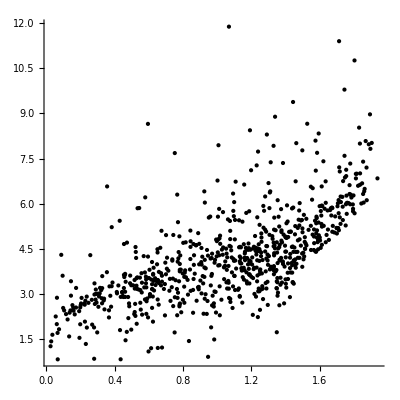

```mathematica
Graphics[Point@cgr,PlotRange->All,AspectRatio->1,Axes->True,AxesOrigin->{0,0},FrameLabel->{"G","E"}]
```

```mathematica
Position[Log@gammaratio,_?(8.1<#&)]
```

{{204},{260},{313}}

```mathematica
Log@gammaratio[[313]]
```

8.17149

```mathematica
gammas[[313]]
```

{-0.0246682,-6.97117×10^-6}

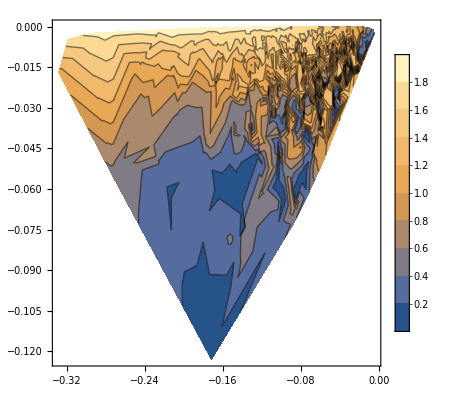

```mathematica
ListContourPlot[gc,PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
S[e_,H_,W_]:=IdentityMatrix[Dimensions[W][[2]]]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e)].W;
```

```mathematica
G[e_,H_,W_]:=Block[{n=Dimensions[W][[2]],Sp,Sn,τy,S},Sp=IdentityMatrix[n]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e*IdentityMatrix[Length[H]])].W;(*Sn=IdentityMatrix[n]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W+e)].W;*)S=(*ArrayFlatten@{{Sp,0},{0,Sp}};*)Sp;τy=KroneckerProduct[IdentityMatrix[n/2],PauliMatrix[2]];n/2-1/2*Tr[S.τy.ConjugateTranspose[S].τy]]
```

```mathematica
Gr[e_,H_,W_]:=Block[{n=Dimensions[W][[2]],Sp,Sn,τy,S},Sp=IdentityMatrix[n]+2π I Transpose[W].Inverse[(H-I *π *W. Transpose@W-e*IdentityMatrix[Length[H]])].W;n/2+Tr[Sp[[1;;n/2,n/2+1;;n]]*ConjugateTranspose[Sp[[1;;n/2,n/2+1;;n]]]]-Tr[Sp[[n/2+1;;n,n/2+1;;n]]*ConjugateTranspose[Sp[[n/2+1;;n,n/2+1;;n]]]]]
```

```mathematica
{H1,W1}=hwlist[[8]];
```

```mathematica
{H2,W2}=hwlist[[2]];
```

```mathematica
S1=S[0,H1,W1]
```

{{0.98773+0. ⅈ,0.044203+0. ⅈ,0.0459433+0. ⅈ,0.0591415+0. ⅈ,0.0994707+0. ⅈ,0.0832605+0. ⅈ},{-0.0602063+0. ⅈ,0.980894+0. ⅈ,0.0787924+0. ⅈ,0.131211+0. ⅈ,0.0904105+0. ⅈ,-0.0512138+0. ⅈ},{-0.0192462+0. ⅈ,-0.0614653+0. ⅈ,0.983816+0. ⅈ,-0.0922499+0. ⅈ,-0.114536+0. ⅈ,-0.0795575+0. ⅈ},{-0.0277371+0. ⅈ,-0.124823+0. ⅈ,0.0529196+0. ⅈ,0.968167+0. ⅈ,-0.177481+0. ⅈ,-0.109556+0. ⅈ},{-0.0856214+0. ⅈ,-0.128562+0. ⅈ,0.0971615+0. ⅈ,0.127893+0. ⅈ,0.954061+0. ⅈ,-0.200278+0. ⅈ},{-0.110876+0. ⅈ,0.00232207+0. ⅈ,0.107455+0. ⅈ,0.13066+0. ⅈ,0.164563+0. ⅈ,0.965402+0. ⅈ}}

```mathematica
Dimensions[W1][[2]]
```

6

```mathematica
S1//Dimensions
```

{6,6}

```mathematica
Tr[S1.Transpose@S1]/2
```

3.+0. ⅈ

```mathematica
S1=S[0,H1,W1];
```

```mathematica
G[0,H1,W1]
```

2.17573+0. ⅈ

```mathematica
enlist=ParallelTable[G[x,H1,W1]//Chop,{x,-2,2,0.01}];
```

```mathematica
enlist2=ParallelTable[G[x,H2,W2]//Chop,{x,-2,2,0.01}];
```

```mathematica
enlist3=ParallelTable[Gr[x,H1,W1]//Chop,{x,-2,2,0.01}];
```

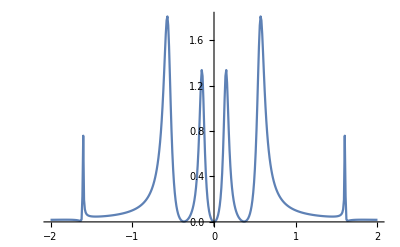

```mathematica
ListLinePlot[enlist,PlotRange->All,DataRange->{-2,2}]
```

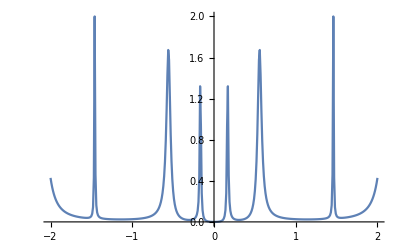

```mathematica
ListLinePlot[enlist2,PlotRange->All,DataRange->{-2,2}]
```

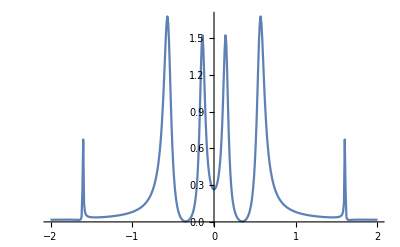

```mathematica
ListLinePlot[enlist3,PlotRange->All,DataRange->{-2,2}]
```

```mathematica
enlist3
```

{2.9853+0.0964062 ⅈ,2.98587+0.0979296 ⅈ,2.98642+0.0994692 ⅈ,2.98694+0.101027 ⅈ,2.98745+0.102606 ⅈ,2.98795+0.104207 ⅈ,2.98843+0.105835 ⅈ,2.9889+0.107491 ⅈ,2.98937+0.109178 ⅈ,2.98982+0.1109 ⅈ,2.99028+0.112661 ⅈ,2.99073+0.114465 ⅈ,2.99118+0.116315 ⅈ,2.99164+0.118219 ⅈ,2.99211+0.12018 ⅈ,2.99258+0.122208 ⅈ,2.99307+0.124308 ⅈ,2.99357+0.126491 ⅈ,2.9941+0.128767 ⅈ,2.99465+0.13115 ⅈ,2.99524+0.133654 ⅈ,2.99586+0.136299 ⅈ,2.99653+0.139107 ⅈ,2.99726+0.142107 ⅈ,2.99806+0.145335 ⅈ,2.99894+0.148836 ⅈ,2.99993+0.152668 ⅈ,3.00105+0.156909 ⅈ,3.00232+0.161663 ⅈ,3.0038+0.167073 ⅈ,3.00554+0.173345 ⅈ,3.00762+0.180776 ⅈ,3.01015+0.189826 ⅈ,3.01331+0.201233 ⅈ,3.01734+0.216269 ⅈ,3.02261+0.23732 ⅈ,3.02964+0.269433 ⅈ,3.03855+0.325354 ⅈ,3.04261+0.447943 ⅈ,2.87495+0.861673 ⅈ,2.10038-0.219196 ⅈ,2.75517-0.142716 ⅈ,2.86714-0.0415486 ⅈ,2.90739+0.00911787 ⅈ,2.92749+0.0392513 ⅈ,2.93939+0.0594282 ⅈ,2.9472+0.0740825 ⅈ,2.95269+0.0853718 ⅈ,2.95675+0.094467 ⅈ,2.95984+0.102057 ⅈ,2.96228+0.108573 ⅈ,2.96423+0.114298 ⅈ,2.96582+0.119428 ⅈ,2.96713+0.124099 ⅈ,2.96822+0.128413 ⅈ,2.96914+0.132443 ⅈ,2.96991+0.136248 ⅈ,2.97056+0.139872 ⅈ,2.97111+0.143349 ⅈ,2.97157+0.146709 ⅈ,2.97196+0.149973 ⅈ,2.97228+0.153162 ⅈ,2.97254+0.15629 ⅈ,2.97275+0.159371 ⅈ,2.97292+0.162417 ⅈ,2.97304+0.165438 ⅈ,2.97312+0.168442 ⅈ,2.97316+0.171437 ⅈ,2.97317+0.17443 ⅈ,2.97314+0.177427 ⅈ,2.97309+0.180435 ⅈ,2.973+0.183457 ⅈ,2.97288+0.1865 ⅈ,2.97274+0.189568 ⅈ,2.97256+0.192664 ⅈ,2.97236+0.195795 ⅈ,2.97214+0.198963 ⅈ,2.97188+0.202173 ⅈ,2.97159+0.205428 ⅈ,2.97128+0.208734 ⅈ,2.97094+0.212093 ⅈ,2.97057+0.21551 ⅈ,2.97017+0.218989 ⅈ,2.96973+0.222534 ⅈ,2.96927+0.22615 ⅈ,2.96877+0.229841 ⅈ,2.96824+0.233611 ⅈ,2.96766+0.237466 ⅈ,2.96705+0.24141 ⅈ,2.9664+0.245449 ⅈ,2.96571+0.249587 ⅈ,2.96497+0.253832 ⅈ,2.96419+0.258189 ⅈ,2.96335+0.262665 ⅈ,2.96246+0.267266 ⅈ,2.96151+0.272001 ⅈ,2.96049+0.276876 ⅈ,2.95941+0.2819 ⅈ,2.95826+0.287083 ⅈ,2.95703+0.292434 ⅈ,2.95572+0.297963 ⅈ,2.95431+0.303682 ⅈ,2.95281+0.309602 ⅈ,2.9512+0.315738 ⅈ,2.94947+0.322102 ⅈ,2.94762+0.328711 ⅈ,2.94562+0.335581 ⅈ,2.94348+0.34273 ⅈ,2.94116+0.350179 ⅈ,2.93865+0.357949 ⅈ,2.93594+0.366064 ⅈ,2.93299+0.37455 ⅈ,2.92979+0.383436 ⅈ,2.9263+0.392753 ⅈ,2.92249+0.402537 ⅈ,2.91832+0.412826 ⅈ,2.91374+0.423663 ⅈ,2.90869+0.435095 ⅈ,2.90311+0.447174 ⅈ,2.89692+0.459957 ⅈ,2.89004+0.47351 ⅈ,2.88234+0.487902 ⅈ,2.87372+0.503212 ⅈ,2.86399+0.519525 ⅈ,2.85299+0.536933 ⅈ,2.84046+0.555537 ⅈ,2.82613+0.575441 ⅈ,2.80964+0.596753 ⅈ,2.79054+0.619573 ⅈ,2.76827+0.643988 ⅈ,2.74214+0.67005 ⅈ,2.71123+0.697743 ⅈ,2.67441+0.726928 ⅈ,2.63021+0.757255 ⅈ,2.5768+0.78801 ⅈ,2.51186+0.817869 ⅈ,2.43265+0.844501 ⅈ,2.33608+0.863961 ⅈ,2.21935+0.869826 ⅈ,2.08125+0.852218 ⅈ,1.92503+0.797344 ⅈ,1.76277+0.689232 ⅈ,1.61955+0.51635 ⅈ,1.53126+0.283659 ⅈ,1.52937+0.0218711 ⅈ,1.61959-0.22103 ⅈ,1.77618-0.405267 ⅈ,1.95981-0.517417 ⅈ,2.13862-0.566825 ⅈ,2.29582-0.571757 ⅈ,2.42652-0.549329 ⅈ,2.53218-0.511985 ⅈ,2.6166-0.467662 ⅈ,2.68389-0.421017 ⅈ,2.7377-0.374607 ⅈ,2.78098-0.329721 ⅈ,2.81607-0.286922 ⅈ,2.84473-0.246359 ⅈ,2.86834-0.207961 ⅈ,2.88792-0.171542 ⅈ,2.90429-0.136858 ⅈ,2.91805-0.103644 ⅈ,2.92967-0.0716245 ⅈ,2.9395-0.0405262 ⅈ,2.94783-0.010075 ⅈ,2.95486+0.0200034 ⅈ,2.96074+0.049989 ⅈ,2.96556+0.0801726 ⅈ,2.96937+0.110864 ⅈ,2.97217+0.142401 ⅈ,2.97389+0.175162 ⅈ,2.97439+0.209578 ⅈ,2.97345+0.246152 ⅈ,2.9707+0.285475 ⅈ,2.9656+0.328256 ⅈ,2.95729+0.375337 ⅈ,2.94451+0.427708 ⅈ,2.92531+0.486484 ⅈ,2.89669+0.552789 ⅈ,2.85397+0.627399 ⅈ,2.79003+0.709826 ⅈ,2.69436+0.796162 ⅈ,2.55347+0.874572 ⅈ,2.35631+0.918093 ⅈ,2.11199+0.881065 ⅈ,1.87604+0.721208 ⅈ,1.73893+0.456625 ⅈ,1.74505+0.179092 ⅈ,1.85246-0.0292977 ⅈ,1.99373-0.151155 ⅈ,2.12742-0.207453 ⅈ,2.23911-0.223387 ⅈ,2.3277-0.216773 ⅈ,2.39644-0.198208 ⅈ,2.44921-0.173573 ⅈ,2.4893-0.14602 ⅈ,2.51925-0.117196 ⅈ,2.54091-0.08792 ⅈ,2.55556-0.0585643 ⅈ,2.56403-0.0292568 ⅈ,2.56681,2.56403+0.0292568 ⅈ,2.55556+0.0585643 ⅈ,2.54091+0.08792 ⅈ,2.51925+0.117196 ⅈ,2.4893+0.14602 ⅈ,2.44921+0.173573 ⅈ,2.39644+0.198208 ⅈ,2.3277+0.216773 ⅈ,2.23911+0.223387 ⅈ,2.12742+0.207453 ⅈ,1.99373+0.151155 ⅈ,1.85246+0.0292977 ⅈ,1.74505-0.179092 ⅈ,1.73893-0.456625 ⅈ,1.87604-0.721208 ⅈ,2.11199-0.881065 ⅈ,2.35631-0.918093 ⅈ,2.55347-0.874572 ⅈ,2.69436-0.796162 ⅈ,2.79003-0.709826 ⅈ,2.85397-0.627399 ⅈ,2.89669-0.552789 ⅈ,2.92531-0.486484 ⅈ,2.94451-0.427708 ⅈ,2.95729-0.375337 ⅈ,2.9656-0.328256 ⅈ,2.9707-0.285475 ⅈ,2.97345-0.246152 ⅈ,2.97439-0.209578 ⅈ,2.97389-0.175162 ⅈ,2.97217-0.142401 ⅈ,2.96937-0.110864 ⅈ,2.96556-0.0801726 ⅈ,2.96074-0.049989 ⅈ,2.95486-0.0200034 ⅈ,2.94783+0.010075 ⅈ,2.9395+0.0405262 ⅈ,2.92967+0.0716245 ⅈ,2.91805+0.103644 ⅈ,2.90429+0.136858 ⅈ,2.88792+0.171542 ⅈ,2.86834+0.207961 ⅈ,2.84473+0.246359 ⅈ,2.81607+0.286922 ⅈ,2.78098+0.329721 ⅈ,2.7377+0.374607 ⅈ,2.68389+0.421017 ⅈ,2.6166+0.467662 ⅈ,2.53218+0.511985 ⅈ,2.42652+0.549329 ⅈ,2.29582+0.571757 ⅈ,2.13862+0.566825 ⅈ,1.95981+0.517417 ⅈ,1.77618+0.405267 ⅈ,1.61959+0.22103 ⅈ,1.52937-0.0218711 ⅈ,1.53126-0.283659 ⅈ,1.61955-0.51635 ⅈ,1.76277-0.689232 ⅈ,1.92503-0.797344 ⅈ,2.08125-0.852218 ⅈ,2.21935-0.869826 ⅈ,2.33608-0.863961 ⅈ,2.43265-0.844501 ⅈ,2.51186-0.817869 ⅈ,2.5768-0.78801 ⅈ,2.63021-0.757255 ⅈ,2.67441-0.726928 ⅈ,2.71123-0.697743 ⅈ,2.74214-0.67005 ⅈ,2.76827-0.643988 ⅈ,2.79054-0.619573 ⅈ,2.80964-0.596753 ⅈ,2.82613-0.575441 ⅈ,2.84046-0.555537 ⅈ,2.85299-0.536933 ⅈ,2.86399-0.519525 ⅈ,2.87372-0.503212 ⅈ,2.88234-0.487902 ⅈ,2.89004-0.47351 ⅈ,2.89692-0.459957 ⅈ,2.90311-0.447174 ⅈ,2.90869-0.435095 ⅈ,2.91374-0.423663 ⅈ,2.91832-0.412826 ⅈ,2.92249-0.402537 ⅈ,2.9263-0.392753 ⅈ,2.92979-0.383436 ⅈ,2.93299-0.37455 ⅈ,2.93594-0.366064 ⅈ,2.93865-0.357949 ⅈ,2.94116-0.350179 ⅈ,2.94348-0.34273 ⅈ,2.94562-0.335581 ⅈ,2.94762-0.328711 ⅈ,2.94947-0.322102 ⅈ,2.9512-0.315738 ⅈ,2.95281-0.309602 ⅈ,2.95431-0.303682 ⅈ,2.95572-0.297963 ⅈ,2.95703-0.292434 ⅈ,2.95826-0.287083 ⅈ,2.95941-0.2819 ⅈ,2.96049-0.276876 ⅈ,2.96151-0.272001 ⅈ,2.96246-0.267266 ⅈ,2.96335-0.262665 ⅈ,2.96419-0.258189 ⅈ,2.96497-0.253832 ⅈ,2.96571-0.249587 ⅈ,2.9664-0.245449 ⅈ,2.96705-0.24141 ⅈ,2.96766-0.237466 ⅈ,2.96824-0.233611 ⅈ,2.96877-0.229841 ⅈ,2.96927-0.22615 ⅈ,2.96973-0.222534 ⅈ,2.97017-0.218989 ⅈ,2.97057-0.21551 ⅈ,2.97094-0.212093 ⅈ,2.97128-0.208734 ⅈ,2.97159-0.205428 ⅈ,2.97188-0.202173 ⅈ,2.97214-0.198963 ⅈ,2.97236-0.195795 ⅈ,2.97256-0.192664 ⅈ,2.97274-0.189568 ⅈ,2.97288-0.1865 ⅈ,2.973-0.183457 ⅈ,2.97309-0.180435 ⅈ,2.97314-0.177427 ⅈ,2.97317-0.17443 ⅈ,2.97316-0.171437 ⅈ,2.97312-0.168442 ⅈ,2.97304-0.165438 ⅈ,2.97292-0.162417 ⅈ,2.97275-0.159371 ⅈ,2.97254-0.15629 ⅈ,2.97228-0.153162 ⅈ,2.97196-0.149973 ⅈ,2.97157-0.146709 ⅈ,2.97111-0.143349 ⅈ,2.97056-0.139872 ⅈ,2.96991-0.136248 ⅈ,2.96914-0.132443 ⅈ,2.96822-0.128413 ⅈ,2.96713-0.124099 ⅈ,2.96582-0.119428 ⅈ,2.96423-0.114298 ⅈ,2.96228-0.108573 ⅈ,2.95984-0.102057 ⅈ,2.95675-0.094467 ⅈ,2.95269-0.0853718 ⅈ,2.9472-0.0740825 ⅈ,2.93939-0.0594282 ⅈ,2.92749-0.0392513 ⅈ,2.90739-0.00911787 ⅈ,2.86714+0.0415486 ⅈ,2.75517+0.142716 ⅈ,2.10038+0.219196 ⅈ,2.87495-0.861673 ⅈ,3.04261-0.447943 ⅈ,3.03855-0.325354 ⅈ,3.02964-0.269433 ⅈ,3.02261-0.23732 ⅈ,3.01734-0.216269 ⅈ,3.01331-0.201233 ⅈ,3.01015-0.189826 ⅈ,3.00762-0.180776 ⅈ,3.00554-0.173345 ⅈ,3.0038-0.167073 ⅈ,3.00232-0.161663 ⅈ,3.00105-0.156909 ⅈ,2.99993-0.152668 ⅈ,2.99894-0.148836 ⅈ,2.99806-0.145335 ⅈ,2.99726-0.142107 ⅈ,2.99653-0.139107 ⅈ,2.99586-0.136299 ⅈ,2.99524-0.133654 ⅈ,2.99465-0.13115 ⅈ,2.9941-0.128767 ⅈ,2.99357-0.126491 ⅈ,2.99307-0.124308 ⅈ,2.99258-0.122208 ⅈ,2.99211-0.12018 ⅈ,2.99164-0.118219 ⅈ,2.99118-0.116315 ⅈ,2.99073-0.114465 ⅈ,2.99028-0.112661 ⅈ,2.98982-0.1109 ⅈ,2.98937-0.109178 ⅈ,2.9889-0.107491 ⅈ,2.98843-0.105835 ⅈ,2.98795-0.104207 ⅈ,2.98745-0.102606 ⅈ,2.98694-0.101027 ⅈ,2.98642-0.0994692 ⅈ,2.98587-0.0979296 ⅈ,2.9853-0.0964062 ⅈ}

```mathematica
enmap=ParallelTable[G[x,(1-α)*H1+(α)*H2,W1],{x,-1,1,0.01},{α,0,1,0.001}];//AbsoluteTiming
```

{84.3041,Null}

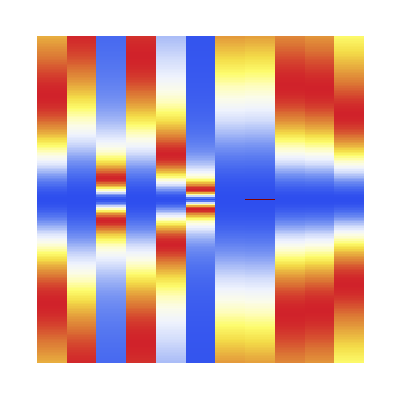

```mathematica
ArrayPlot[enmap,AspectRatio->1,ColorFunction->"TemperatureMap"]
```

```mathematica
ArrayPlot[Re@enmap,ColorFunction->"TemperatureMap",DataRange->{{0,1},{-2,2}},PlotLegends->Automatic,PlotRange->Full,AspectRatio->1,FrameTicks->True(*,Epilog->{ First@Out[342]}*)]
```

-Graphics-

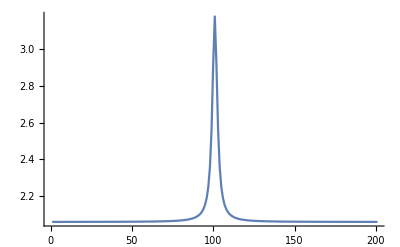

```mathematica
ListPlot[enmap[[All,1]],PlotRange->Full,Joined->True]
```

```mathematica
eiglist=ParallelTable[Eigenvalues[(1-α)*H1+(α)*H2],{α,0,1,0.01}]
```

{{-50.7607,50.7607,48.1955,-48.1955,-46.9632,46.9632,-46.3001,46.3001,45.179,-45.179,43.7896,-43.7896,-42.7785,42.7785,-41.5504,41.5504,40.6976,-40.6976,39.4286,-39.4286,38.7188,-38.7188,37.7078,74,8.26621,7.25652,-7.25652,-6.55754,6.55754,-5.90729,5.90729,5.35926,-5.35926,4.62369,-4.62369,3.68402,-3.68402,-3.16041,3.16041,2.62033,-2.62033,-2.01433,2.01433,0.838845,-0.838845,-0.0131341,0.0131341},99,{1}}
 |  |  |  |

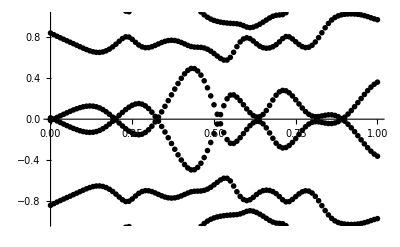

```mathematica
ListPlot[Transpose@eiglist,DataRange->{0,1},PlotRange->{All,{-1,1}},PlotStyle->Directive[PointSize[.01],Black]]
```

```mathematica
x1=RandomVariate[NormalDistribution[],10000];
```

```mathematica
x2=RandomVariate[NormalDistribution[],10000];
```

```mathematica
smd1=(First@SmoothHistogram[x1])[[2,1,3,3,1]];
```

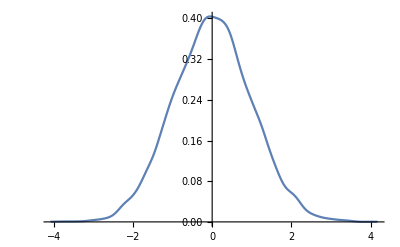

```mathematica
SmoothHistogram[x1]
```

```mathematica
smd2=(First@SmoothHistogram[x2])[[2,1,3,3,1]];
```

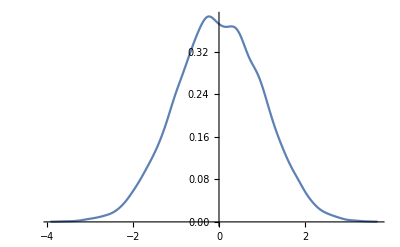

```mathematica
SmoothHistogram[x2]
```

```mathematica
smd3=(First@SmoothHistogram[(x1-x2)/√2])[[2,1,3,3,1]];
```

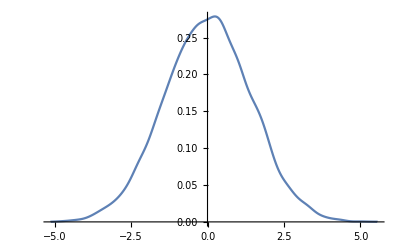

```mathematica
SmoothHistogram[x1-x2]
```

```mathematica
FindFit[smd1,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.400163,b→0.995801}

```mathematica
FindFit[smd2,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.389227,b→1.02993}

```mathematica
FindFit[smd3,a*Exp[-x^2/(2 b^2)],{a,b},x]
```

{a→0.393453,b→1.01524}